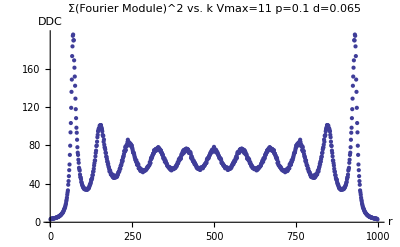

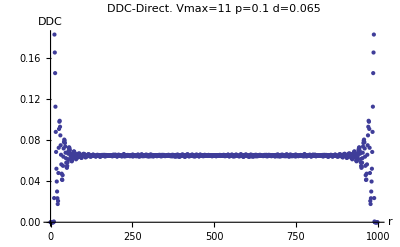

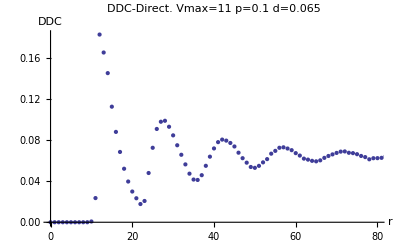

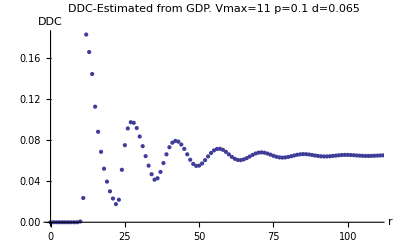

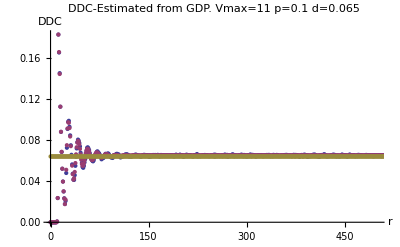

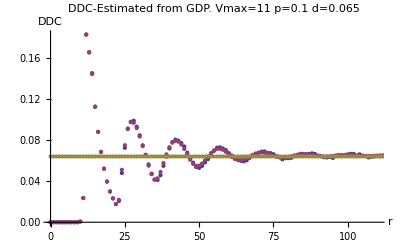

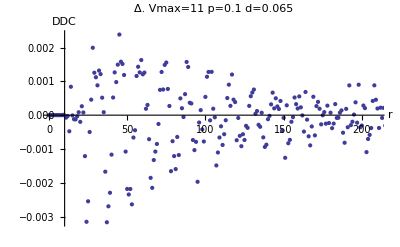

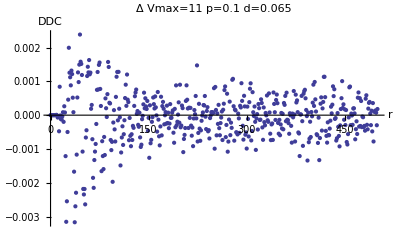

1000. = L

65 = N

0.0640641 = (N-1)/(L-1)

32. = (N-1)/2

31.9674  : Sum of DDC-Half Track

31.9954  : Sum of OZ-Half Track

-0.0280016  : Sum of Δ

0.0661785  : DDC-Averaged around L/2

0.0661818  : OZ-Averaged around L/2

1.00005  : Ratio at Half Track

0.0000515677  : Δ at half track over random value

0.014458 = Mean of first 5*vmax values/Random Mean of DDC

3  : First time Δ becomes 0

```mathematica
d="0.065";
p="0.1";
vmax="11";
n=1000.000;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*n];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,n}];
m2=(m-1)/2.;  
fourier="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine1000/fourier.1d.averaged.d";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine1000/DDCCheck.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/fine1000/ddensitycorrelation.d";
g=".p"<>p<>".v11.txt";
fourieradd=fourier<>d<>g;
ddccadd=ddcc<>d<>g;
ddcadd=ddc<>d<>g;
Fou=ReadList[fourieradd,{Number,Number}];
DDCC=ReadList[ddccadd,{Number,Number}];
DDC=ReadList[ddcadd,{Number,Number}];
ListPlot[Fou,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
ListPlot[DDC,PlotLabel->"DDC-Direct.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,80},Full}]
ListPlot[DDCC,PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
ListPlot[{DDC,DDCC,random},PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,n/2},Full}]
ListPlot[{DDC,DDCC,random},PlotLabel->"DDC-Estimated from GDP.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{0,110},Full}]
DDC2=DDC[[All,2]];
DDCC2=DDCC[[All,2]];
dif=Table[{i-1,DDC2[[i]]-DDCC2[[i]]},{i,1,n/2+1}];
dif2=dif[[All,2]];
ListPlot[dif,PlotLabel->"Δ.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->{{1,210},Full}]
ListPlot[dif,PlotLabel->"Δ  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"DDC"},PlotRange->Full]
n "= L"
m  "= N  "
prand  "= (N-1)/(L-1)"
m2 "= (N-1)/2"
Sum[DDC2[[i]],{i,1,n/2}] " : Sum of DDC-Half Track"
Sum[DDCC2[[i]],{i,1,n/2}]  " : Sum of OZ-Half Track"
Sum[dif2[[i]],{i,1,n/2}]  " : Sum of Δ"
DDCF=Sum[DDC2[[i]],{i,n/2-5*11,n/2}]/(5*11);
DDCF  " : DDC-Averaged around L/2"
DDCCF=Sum[DDCC2[[i]],{i,n/2-5*11,n/2}]/(5*11);
DDCCF " : OZ-Averaged around L/2"
DDCCF/DDCF " : Ratio at Half Track"
(DDCCF-DDCF)/prand  " : Δ at half track over random value"
diff=Table[{i,(DDC2[[i]]-DDCC2[[i]])},{i,0,n/2}];
diff2=diff[[All,2]];
sum=Sum[Abs[diff2[[i]]],{i,1,55}]/(55);
sum/prand  "= Mean of first 5*vmax values/Random Mean of DDC"
x=3; While[dif2[[x]]>0.00005,x++]
x " : First time Δ becomes 0"
RHT=Append[RHT,{o,DDCCF/DDCF}];
DHTOR=Append[DHTOR,{o,(DDCCF-DDCF)/prand }];
MFVOR=Append[MFVOR,{o,sum/prand}];
FTDBZ=Append[FTDBZ,{o,x}];
```

```mathematica
RHT=Append[RHT,{o,DDCCF/DDCF}];
DHTOR=Append[DHTOR,{o,(DDCCF-DDCF)/prand }];
MFVOR=Append[MFVOR,{o,sum/prand}];
FTDBZ=Append[FTDBZ,{o,x}];
```

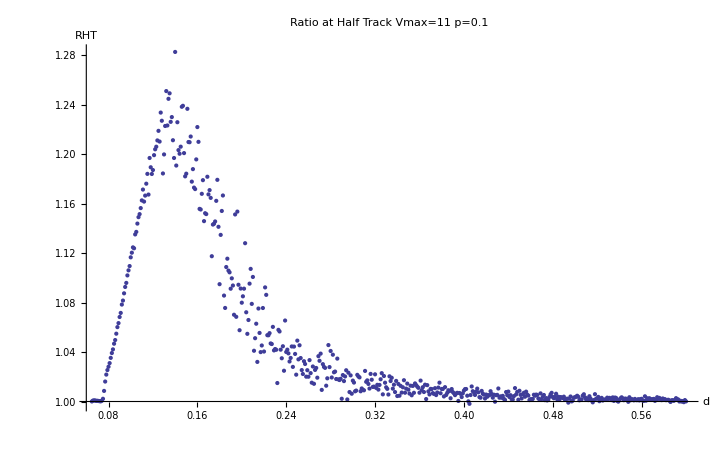

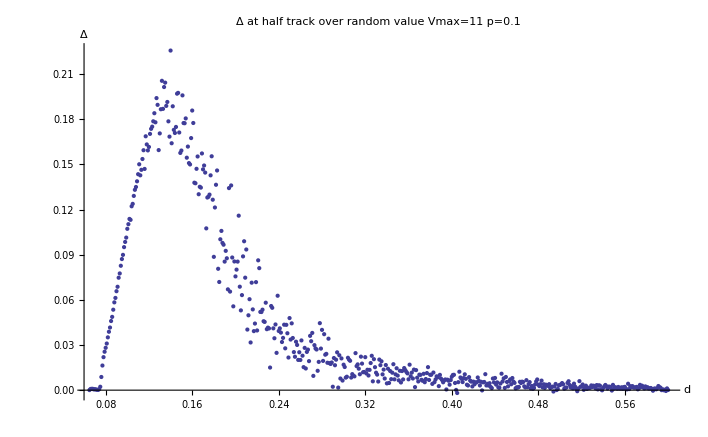

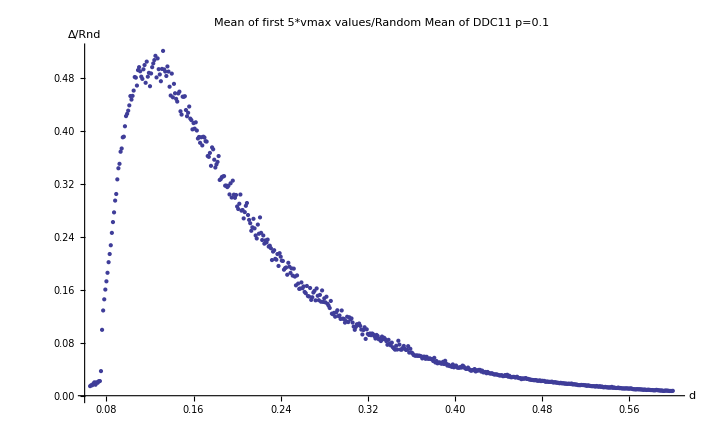

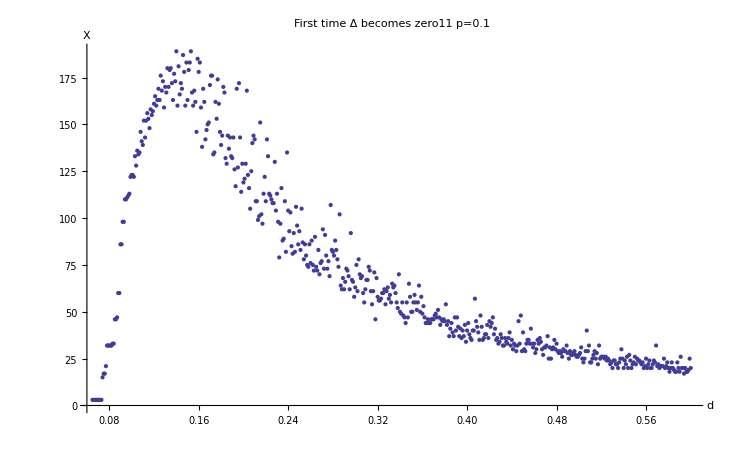

```mathematica
ListPlot[RHT,PlotLabel->"Ratio at Half Track  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","RHT"},PlotRange->Full]
ListPlot[DHTOR,PlotLabel->"Δ at half track over random value  Vmax="<>vmax<>"  p="<>p,AxesLabel->{"d","Δ"},PlotRange->Full]
ListPlot[MFVOR ,PlotLabel->"Mean of first 5*vmax values/Random Mean of DDC"<>vmax<>"  p="<>p,AxesLabel->{"d","Δ/Rnd"},PlotRange->Full]
ListPlot[FTDBZ,PlotLabel->"First time Δ becomes zero"<>vmax<>"  p="<>p,AxesLabel->{"d","X"},PlotRange->Full]
```

```mathematica
RHT
DHTOR
MFVOR
FTDBZ
```

{{0.065,1.00005},{0.066,1.00076},{0.067,1.00085},{0.068,1.00084},{0.069,1.00048},{0.07,1.00061},{0.071,1.00042},{0.072,1.00025},{0.073,1.00014},{0.074,1.00062},{0.075,1.00219},{0.076,1.00856},{0.077,1.01613},{0.078,1.02174},{0.079,1.02541},{0.08,1.02809},{0.081,1.03101},{0.082,1.03527},{0.083,1.03916},{0.084,1.04212},{0.085,1.0467},{0.086,1.04966},{0.087,1.0548},{0.088,1.06011},{0.089,1.06335},{0.09,1.06829},{0.091,1.07158},{0.092,1.07834},{0.093,1.08158},{0.094,1.08742},{0.095,1.09258},{0.096,1.09584},{0.097,1.1019},{0.098,1.106},{0.099,1.10945},{0.1,1.1165},{0.101,1.12026},{0.102,1.12456},{0.103,1.12382},{0.104,1.13502},{0.105,1.13707},{0.106,1.14378},{0.107,1.14898},{0.108,1.15142},{0.109,1.15631},{0.11,1.16252},{0.111,1.17128},{0.112,1.16156},{0.113,1.1664},{0.114,1.17602},{0.115,1.18396},{0.116,1.16723},{0.117,1.19679},{0.118,1.18929},{0.119,1.18387},{0.12,1.18704},{0.121,1.19909},{0.122,1.20382},{0.123,1.20591},{0.124,1.21098},{0.125,1.21872},{0.126,1.21006},{0.127,1.23348},{0.128,1.22688},{0.129,1.18429},{0.13,1.19966},{0.131,1.22266},{0.132,1.25087},{0.133,1.22306},{0.134,1.24461},{0.135,1.24906},{0.136,1.226},{0.137,1.22985},{0.138,1.21114},{0.139,1.19679},{0.14,1.2825},{0.141,1.19069},{0.142,1.22569},{0.143,1.20315},{0.144,1.20023},{0.145,1.20593},{0.146,1.23817},{0.147,1.23896},{0.148,1.20074},{0.149,1.18195},{0.15,1.18411},{0.151,1.23654},{0.152,1.2097},{0.153,1.20953},{0.154,1.21413},{0.155,1.17769},{0.156,1.18779},{0.157,1.17286},{0.158,1.17166},{0.159,1.19565},{0.16,1.22178},{0.161,1.20984},{0.162,1.15567},{0.163,1.15516},{0.164,1.16784},{0.165,1.17887},{0.166,1.14576},{0.167,1.15216},{0.168,1.15146},{0.169,1.18163},{0.17,1.16738},{0.171,1.17082},{0.172,1.16456},{0.173,1.11741},{0.174,1.143},{0.175,1.14364},{0.176,1.1455},{0.177,1.16216},{0.178,1.17914},{0.179,1.14119},{0.18,1.09481},{0.181,1.13465},{0.182,1.15398},{0.183,1.16649},{0.184,1.0856},{0.185,1.0756},{0.186,1.10868},{0.187,1.11542},{0.188,1.1058},{0.189,1.10438},{0.19,1.09115},{0.191,1.09954},{0.192,1.09374},{0.193,1.0701},{0.194,1.15117},{0.195,1.06844},{0.196,1.15346},{0.197,1.09435},{0.198,1.05761},{0.199,1.09128},{0.2,1.07985},{0.201,1.08501},{0.202,1.09118},{0.203,1.12793},{0.204,1.0721},{0.205,1.05469},{0.206,1.06586},{0.207,1.09524},{0.208,1.10717},{0.209,1.07889},{0.21,1.10066},{0.211,1.04101},{0.212,1.05115},{0.213,1.06286},{0.214,1.03199},{0.215,1.07514},{0.216,1.05542},{0.217,1.03991},{0.218,1.04527},{0.219,1.07555},{0.22,1.04039},{0.221,1.09221},{0.222,1.08618},{0.223,1.0536},{0.224,1.05353},{0.225,1.05524},{0.226,1.04692},{0.227,1.04645},{0.228,1.06031},{0.229,1.0413},{0.23,1.04239},{0.231,1.04182},{0.232,1.01492},{0.233,1.0579},{0.234,1.0566},{0.235,1.04189},{0.236,1.03494},{0.237,1.04465},{0.238,1.02486},{0.239,1.06544},{0.24,1.04004},{0.241,1.0419},{0.242,1.03889},{0.243,1.03233},{0.244,1.03519},{0.245,1.04448},{0.246,1.02797},{0.247,1.04438},{0.248,1.03845},{0.249,1.02168},{0.25,1.04921},{0.251,1.03405},{0.252,1.04544},{0.253,1.03512},{0.254,1.02539},{0.255,1.02223},{0.256,1.03255},{0.257,1.03031},{0.258,1.02008},{0.259,1.02529},{0.26,1.02002},{0.261,1.03345},{0.262,1.02294},{0.263,1.01521},{0.264,1.02829},{0.265,1.01431},{0.266,1.02552},{0.267,1.02711},{0.268,1.01925},{0.269,1.03663},{0.27,1.0329},{0.271,1.03869},{0.272,1.00937},{0.273,1.03018},{0.274,1.02793},{0.275,1.02718},{0.276,1.01277},{0.277,1.01874},{0.278,1.0456},{0.279,1.02781},{0.28,1.04085},{0.281,1.0194},{0.282,1.03782},{0.283,1.02362},{0.284,1.02419},{0.285,1.01817},{0.286,1.03467},{0.287,1.01788},{0.288,1.01735},{0.289,1.01835},{0.29,1.00223},{0.291,1.02137},{0.292,1.01649},{0.293,1.02024},{0.294,1.02525},{0.295,1.00167},{0.296,1.02326},{0.297,1.00764},{0.298,1.02111},{0.299,1.00629},{0.3,1.01687},{0.301,1.0153},{0.302,1.00823},{0.303,1.00882},{0.304,1.02154},{0.305,1.02025},{0.306,1.01948},{0.307,1.00827},{0.308,1.01054},{0.309,1.00939},{0.31,1.00906},{0.311,1.02471},{0.312,1.01591},{0.313,1.01707},{0.314,1.01419},{0.315,1.01046},{0.316,1.0223},{0.317,1.01759},{0.318,1.0118},{0.319,1.012},{0.32,1.02197},{0.321,1.011},{0.322,1.01346},{0.323,1.00963},{0.324,1.01338},{0.325,1.01798},{0.326,1.0229},{0.327,1.00578},{0.328,1.02058},{0.329,1.01518},{0.33,1.0115},{0.331,1.01022},{0.332,1.00565},{0.333,1.02034},{0.334,1.01654},{0.335,1.01916},{0.336,1.01039},{0.337,1.01359},{0.338,1.00763},{0.339,1.01663},{0.34,1.00443},{0.341,1.01415},{0.342,1.00469},{0.343,1.01264},{0.344,1.00722},{0.345,1.0115},{0.346,1.01719},{0.347,1.00709},{0.348,1.0104},{0.349,1.01448},{0.35,1.00957},{0.351,1.00643},{0.352,1.01278},{0.353,1.00503},{0.354,1.0126},{0.355,1.00703},{0.356,1.01461},{0.357,1.01325},{0.358,1.01203},{0.359,1.01106},{0.36,1.00712},{0.361,1.01689},{0.362,1.00919},{0.363,1.01157},{0.364,1.00766},{0.365,1.01358},{0.366,1.00199},{0.367,1.01322},{0.368,1.00817},{0.369,1.0057},{0.37,1.0102},{0.371,1.01007},{0.372,1.00678},{0.373,1.00616},{0.374,1.01077},{0.375,1.0052},{0.376,1.00729},{0.377,1.01125},{0.378,1.01522},{0.379,1.00667},{0.38,1.01014},{0.381,1.01013},{0.382,1.0041},{0.383,1.0116},{0.384,1.00524},{0.385,1.00703},{0.386,1.0091},{0.387,1.00843},{0.388,1.00262},{0.389,1.01006},{0.39,1.00763},{0.391,1.00664},{0.392,1.00514},{0.393,1.00637},{0.394,1.00701},{0.395,1.00045},{0.396,1.00687},{0.397,1.00619},{0.398,1.00358},{0.399,1.00662},{0.4,1.00881},{0.401,1.01001},{0.402,1.0101},{0.403,1.00469},{0.404,1.00014},{0.405,0.998144},{0.406,1.00523},{0.407,1.01216},{0.408,1.00833},{0.409,1.00744},{0.41,1.00529},{0.411,1.00792},{0.412,1.01042},{0.413,1.00744},{0.414,1.00355},{0.415,1.00306},{0.416,1.00856},{0.417,1.00627},{0.418,1.00558},{0.419,1.00241},{0.42,1.00559},{0.421,1.00383},{0.422,1.0051},{0.423,1.00511},{0.424,1.00833},{0.425,1.00606},{0.426,1.00308},{0.427,1.00548},{0.428,0.999834},{0.429,1.0051},{0.43,1.00536},{0.431,1.01053},{0.432,1.00308},{0.433,1.00416},{0.434,1.00302},{0.435,1.00455},{0.436,1.00207},{0.437,1.00134},{0.438,1.00765},{0.439,1.0051},{0.44,1.00801},{0.441,1.00362},{0.442,1.00509},{0.443,1.00183},{0.444,1.00161},{0.445,1.00434},{0.446,1.01084},{0.447,1.00569},{0.448,1.00775},{0.449,1.00147},{0.45,1.00867},{0.451,1.00537},{0.452,1.00248},{0.453,1.00587},{0.454,1.00704},{0.455,1.00386},{0.456,1.00796},{0.457,1.0056},{0.458,1.00475},{0.459,1.00117},{0.46,1.00187},{0.461,1.0017},{0.462,1.00208},{0.463,1.00546},{0.464,1.00467},{0.465,1.00555},{0.466,1.00532},{0.467,1.00251},{0.468,1.00178},{0.469,1.00656},{0.47,1.00192},{0.471,1.00388},{0.472,1.00527},{0.473,1.00111},{0.474,1.00275},{0.475,1.00087},{0.476,1.00139},{0.477,1.00365},{0.478,1.0057},{0.479,1.00702},{0.48,1.0036},{0.481,1.00262},{0.482,1.00393},{0.483,1.00626},{0.484,1.00175},{0.485,1.00386},{0.486,1.00147},{0.487,1.00357},{0.488,1.00323},{0.489,1.00278},{0.49,1.00391},{0.491,1.00137},{0.492,1.00192},{0.493,1.00231},{0.494,0.999108},{0.495,1.00235},{0.496,1.00405},{0.497,1.00008},{0.498,1.0008},{0.499,1.00313},{0.5,1.0034},{0.501,1.00384},{0.502,1.00464},{0.503,1.00378},{0.504,1.00098},{0.505,1.00154},{0.506,1.00173},{0.507,1.00472},{0.508,1.00585},{0.509,1.00337},{0.51,1.0017},{0.511,1.00253},{0.512,1.00114},{0.513,1.00427},{0.514,1.00232},{0.515,1.00088},{0.516,0.99932},{0.517,1.00114},{0.518,1.00591},{0.519,1.00219},{0.52,1.00244},{0.521,1.00371},{0.522,1.00024},{0.523,1.00173},{0.524,1.00293},{0.525,1.0008},{0.526,1.00159},{0.527,1.00146},{0.528,1.00158},{0.529,1.0031},{0.53,1.00207},{0.531,1.00293},{0.532,1.00231},{0.533,1.00115},{0.534,1.00332},{0.535,1.0005},{0.536,1.00315},{0.537,1.00291},{0.538,1.00053},{0.539,0.999898},{0.54,1.00146},{0.541,1.0025},{0.542,1.0034},{0.543,1.00246},{0.544,1.00108},{0.545,1.00231},{0.546,1.00222},{0.547,1.0018},{0.548,0.999749},{0.549,1.00345},{0.55,1.00103},{0.551,1.00192},{0.552,1.00159},{0.553,1.00094},{0.554,1.00209},{0.555,1.00112},{0.556,1.00107},{0.557,1.00187},{0.558,1.00085},{0.559,1.00193},{0.56,1.00217},{0.561,1.00073},{0.562,1.0005},{0.563,1.0042},{0.564,1.0007},{0.565,1.00262},{0.566,1.00192},{0.567,1.00265},{0.568,1.00172},{0.569,1.00174},{0.57,1.00179},{0.571,1.00211},{0.572,1.00054},{0.573,1.00117},{0.574,1.00346},{0.575,1.00209},{0.576,1.0029},{0.577,1.00197},{0.578,1.0011},{0.579,1.00245},{0.58,1.00161},{0.581,1.00192},{0.582,1.00109},{0.583,1.0012},{0.584,1.00142},{0.585,1.00077},{0.586,0.999632},{0.587,1.00095},{0.588,1.00106},{0.589,1.00055},{0.59,1.00131},{0.591,1.0027},{0.592,1.00187},{0.593,1.00162},{0.594,1.00001},{0.595,1.00057},{0.596,0.999933},{0.597,1.00031},{0.598,0.999466},{0.599,1.00114},{0.6,1.00011}}

{{0.065,0.0000515677},{0.066,0.000780701},{0.067,0.000873258},{0.068,0.000865077},{0.069,0.000490044},{0.07,0.000625803},{0.071,0.000428273},{0.072,0.000260021},{0.073,0.000143619},{0.074,0.000643515},{0.075,0.00225619},{0.076,0.00875109},{0.077,0.0163591},{0.078,0.0219224},{0.079,0.0255246},{0.08,0.0281434},{0.081,0.0309786},{0.082,0.0350771},{0.083,0.0388001},{0.084,0.0416095},{0.085,0.045922},{0.086,0.0486903},{0.087,0.0534624},{0.088,0.0583348},{0.089,0.0612853},{0.09,0.0657479},{0.091,0.0687006},{0.092,0.0747111},{0.093,0.0775519},{0.094,0.0826541},{0.095,0.0871075},{0.096,0.0898959},{0.097,0.09504},{0.098,0.0984919},{0.099,0.101368},{0.1,0.107211},{0.101,0.110288},{0.102,0.113776},{0.103,0.113169},{0.104,0.122177},{0.105,0.123791},{0.106,0.12908},{0.107,0.133131},{0.108,0.135014},{0.109,0.13877},{0.11,0.1435},{0.111,0.150097},{0.112,0.142751},{0.113,0.146406},{0.114,0.153592},{0.115,0.159431},{0.116,0.147},{0.117,0.168695},{0.118,0.163276},{0.119,0.159316},{0.12,0.161618},{0.121,0.170288},{0.122,0.173638},{0.123,0.175103},{0.124,0.178656},{0.125,0.184023},{0.126,0.177984},{0.127,0.194066},{0.128,0.189581},{0.129,0.159519},{0.13,0.170603},{0.131,0.186662},{0.132,0.205555},{0.133,0.186916},{0.134,0.201414},{0.135,0.204335},{0.136,0.188892},{0.137,0.1915},{0.138,0.178618},{0.139,0.168463},{0.14,0.225663},{0.141,0.164064},{0.142,0.188623},{0.143,0.172958},{0.144,0.170879},{0.145,0.174902},{0.146,0.197006},{0.147,0.197527},{0.148,0.171206},{0.149,0.157641},{0.15,0.159217},{0.151,0.195875},{0.152,0.177492},{0.153,0.177366},{0.154,0.180568},{0.155,0.154463},{0.156,0.16185},{0.157,0.150874},{0.158,0.149973},{0.159,0.167495},{0.16,0.185801},{0.161,0.177525},{0.162,0.137862},{0.163,0.137472},{0.164,0.147081},{0.165,0.155274},{0.166,0.130185},{0.167,0.135142},{0.168,0.134598},{0.169,0.157283},{0.17,0.146708},{0.171,0.149273},{0.172,0.144576},{0.173,0.107498},{0.174,0.127994},{0.175,0.128491},{0.176,0.129939},{0.177,0.142735},{0.178,0.155407},{0.179,0.126549},{0.18,0.0885803},{0.181,0.12138},{0.182,0.136475},{0.183,0.145974},{0.184,0.0806456},{0.185,0.0718804},{0.186,0.100249},{0.187,0.105816},{0.188,0.0978436},{0.189,0.0966459},{0.19,0.085422},{0.191,0.0925659},{0.192,0.0876329},{0.193,0.0669805},{0.194,0.134262},{0.195,0.0654956},{0.196,0.136024},{0.197,0.0881408},{0.198,0.0556869},{0.199,0.0855084},{0.2,0.0755885},{0.201,0.0800956},{0.202,0.0854149},{0.203,0.115938},{0.204,0.0687462},{0.205,0.0530037},{0.206,0.0631564},{0.207,0.0888837},{0.208,0.0989355},{0.209,0.0747352},{0.21,0.0934685},{0.211,0.0402621},{0.212,0.0497337},{0.213,0.0604391},{0.214,0.0316823},{0.215,0.0714189},{0.216,0.0536557},{0.217,0.0392206},{0.218,0.0442583},{0.219,0.071776},{0.22,0.039664},{0.221,0.086265},{0.222,0.0810706},{0.223,0.0519768},{0.224,0.051916},{0.225,0.0534803},{0.226,0.0457917},{0.227,0.0453507},{0.228,0.0581095},{0.229,0.0405189},{0.23,0.0415425},{0.231,0.0410113},{0.232,0.0150183},{0.233,0.0559104},{0.234,0.0547219},{0.235,0.0410702},{0.236,0.0344858},{0.237,0.0436559},{0.238,0.0247798},{0.239,0.0627367},{0.24,0.0393238},{0.241,0.041078},{0.242,0.0382337},{0.243,0.0319852},{0.244,0.0347217},{0.245,0.0434983},{0.246,0.0277885},{0.247,0.0433982},{0.248,0.037811},{0.249,0.0216747},{0.25,0.0478942},{0.251,0.0336274},{0.252,0.0443909},{0.253,0.0346515},{0.254,0.0252859},{0.255,0.0222058},{0.256,0.0321926},{0.257,0.0300371},{0.258,0.020096},{0.259,0.0251854},{0.26,0.0200447},{0.261,0.0330448},{0.262,0.022899},{0.263,0.0152925},{0.264,0.0280895},{0.265,0.014402},{0.266,0.0254049},{0.267,0.0269529},{0.268,0.0192847},{0.269,0.0360752},{0.27,0.0325178},{0.271,0.0380262},{0.272,0.00948149},{0.273,0.0299092},{0.274,0.0277369},{0.275,0.0270138},{0.276,0.0128692},{0.277,0.0187817},{0.278,0.0445211},{0.279,0.0276222},{0.28,0.0400593},{0.281,0.0194311},{0.282,0.0371947},{0.283,0.0235525},{0.284,0.0241086},{0.285,0.0182161},{0.286,0.0342002},{0.287,0.0179264},{0.288,0.0174096},{0.289,0.0183917},{0.29,0.00226844},{0.291,0.0213515},{0.292,0.0165567},{0.293,0.0202474},{0.294,0.025132},{0.295,0.00169731},{0.296,0.0231987},{0.297,0.00773703},{0.298,0.0211039},{0.299,0.00637915},{0.3,0.0169272},{0.301,0.0153781},{0.302,0.00832999},{0.303,0.00892159},{0.304,0.021517},{0.305,0.0202582},{0.306,0.0195032},{0.307,0.00836898},{0.308,0.0106409},{0.309,0.00949268},{0.31,0.00916006},{0.311,0.0246056},{0.312,0.015977},{0.313,0.017125},{0.314,0.0142746},{0.315,0.0105619},{0.316,0.022261},{0.317,0.0176412},{0.318,0.0118952},{0.319,0.012099},{0.32,0.0219318},{0.321,0.0111025},{0.322,0.013555},{0.323,0.00972928},{0.324,0.0134761},{0.325,0.0180179},{0.326,0.0228386},{0.327,0.00586312},{0.328,0.0205768},{0.329,0.0152564},{0.33,0.0115964},{0.331,0.0103232},{0.332,0.00572994},{0.333,0.0203368},{0.334,0.0166046},{0.335,0.0191825},{0.336,0.0104928},{0.337,0.0136741},{0.338,0.00772607},{0.339,0.0166888},{0.34,0.00450126},{0.341,0.0142343},{0.342,0.00476452},{0.343,0.012732},{0.344,0.00731476},{0.345,0.0116012},{0.346,0.0172437},{0.347,0.00718561},{0.348,0.010502},{0.349,0.0145562},{0.35,0.00967404},{0.351,0.00651364},{0.352,0.0128729},{0.353,0.00510857},{0.354,0.0126897},{0.355,0.00712307},{0.356,0.0146893},{0.357,0.0133412},{0.358,0.0121284},{0.359,0.011154},{0.36,0.00720717},{0.361,0.0169368},{0.362,0.0092873},{0.363,0.0116663},{0.364,0.00775467},{0.365,0.0136674},{0.366,0.00202064},{0.367,0.0133102},{0.368,0.00826584},{0.369,0.00577614},{0.37,0.0103},{0.371,0.0101634},{0.372,0.00686953},{0.373,0.00624272},{0.374,0.01087},{0.375,0.0052779},{0.376,0.00738553},{0.377,0.0113458},{0.378,0.0152942},{0.379,0.00675788},{0.38,0.0102378},{0.381,0.0102246},{0.382,0.00416152},{0.383,0.0116974},{0.384,0.00531919},{0.385,0.00712218},{0.386,0.00919212},{0.387,0.00852834},{0.388,0.00266231},{0.389,0.0101591},{0.39,0.00772244},{0.391,0.00672683},{0.392,0.00521779},{0.393,0.00645411},{0.394,0.00709986},{0.395,0.000458332},{0.396,0.00695801},{0.397,0.0062754},{0.398,0.00364009},{0.399,0.00670316},{0.4,0.00890096},{0.401,0.0101033},{0.402,0.0101953},{0.403,0.00476176},{0.404,0.000145895},{0.405,-0.00189635},{0.406,0.00530288},{0.407,0.0122499},{0.408,0.00841949},{0.409,0.00753372},{0.41,0.00536747},{0.411,0.0080165},{0.412,0.0105194},{0.413,0.0075287},{0.414,0.00360612},{0.415,0.00311419},{0.416,0.00865276},{0.417,0.00635705},{0.418,0.00566096},{0.419,0.00245505},{0.42,0.0056648},{0.421,0.00388572},{0.422,0.00516861},{0.423,0.00517961},{0.424,0.00842046},{0.425,0.00614102},{0.426,0.00312684},{0.427,0.00555667},{0.428,-0.000168832},{0.429,0.00517685},{0.43,0.00543508},{0.431,0.0106189},{0.432,0.00312996},{0.433,0.00421897},{0.434,0.00307146},{0.435,0.00461712},{0.436,0.00210945},{0.437,0.00136565},{0.438,0.00774},{0.439,0.00517734},{0.44,0.00810437},{0.441,0.00368206},{0.442,0.00516502},{0.443,0.00186259},{0.444,0.00163887},{0.445,0.00440464},{0.446,0.0109304},{0.447,0.00577021},{0.448,0.00784186},{0.449,0.00149558},{0.45,0.0087643},{0.451,0.00544744},{0.452,0.00252172},{0.453,0.00594574},{0.454,0.00712339},{0.455,0.00392231},{0.456,0.00805256},{0.457,0.00567749},{0.458,0.00482262},{0.459,0.00119602},{0.46,0.00190766},{0.461,0.0017276},{0.462,0.00212065},{0.463,0.00553456},{0.464,0.00473326},{0.465,0.00563061},{0.466,0.00539917},{0.467,0.00255343},{0.468,0.00180975},{0.469,0.00664669},{0.47,0.00195668},{0.471,0.00393764},{0.472,0.00534134},{0.473,0.00112753},{0.474,0.00279847},{0.475,0.000886914},{0.476,0.00141615},{0.477,0.00371004},{0.478,0.00577554},{0.479,0.00710696},{0.48,0.0036592},{0.481,0.0026637},{0.482,0.00398852},{0.483,0.00634103},{0.484,0.00177582},{0.485,0.00392305},{0.486,0.00149219},{0.487,0.00362619},{0.488,0.00328001},{0.489,0.00282541},{0.49,0.00396829},{0.491,0.00139193},{0.492,0.00195616},{0.493,0.00234721},{0.494,-0.000910024},{0.495,0.00239186},{0.496,0.00411471},{0.497,0.0000782208},{0.498,0.000816998},{0.499,0.00317605},{0.5,0.0034583},{0.501,0.00390286},{0.502,0.00471196},{0.503,0.00383408},{0.504,0.00100088},{0.505,0.00157177},{0.506,0.00176166},{0.507,0.00478565},{0.508,0.00592582},{0.509,0.00342438},{0.51,0.00172476},{0.511,0.00257283},{0.512,0.00116418},{0.513,0.00432922},{0.514,0.00236297},{0.515,0.000899418},{0.516,-0.000693216},{0.517,0.00116142},{0.518,0.00598778},{0.519,0.00222512},{0.52,0.00248026},{0.521,0.00377032},{0.522,0.00024317},{0.523,0.00175756},{0.524,0.00298054},{0.525,0.000813967},{0.526,0.001613},{0.527,0.00148849},{0.528,0.00160316},{0.529,0.00314809},{0.53,0.00210818},{0.531,0.00297897},{0.532,0.00234855},{0.533,0.00117193},{0.534,0.00336978},{0.535,0.000511847},{0.536,0.00319986},{0.537,0.00295918},{0.538,0.000543928},{0.539,-0.000104019},{0.54,0.00148349},{0.541,0.00254052},{0.542,0.00345331},{0.543,0.00250005},{0.544,0.00109637},{0.545,0.00234408},{0.546,0.00226162},{0.547,0.00183117},{0.548,-0.00025542},{0.549,0.0035019},{0.55,0.00105147},{0.551,0.00195771},{0.552,0.00161419},{0.553,0.000955861},{0.554,0.00212482},{0.555,0.00113831},{0.556,0.00108874},{0.557,0.00190623},{0.558,0.000863409},{0.559,0.00196727},{0.56,0.00220199},{0.561,0.000740752},{0.562,0.000508841},{0.563,0.00426619},{0.564,0.000717448},{0.565,0.00266542},{0.566,0.00195531},{0.567,0.00269297},{0.568,0.0017504},{0.569,0.00177316},{0.57,0.00181617},{0.571,0.00214984},{0.572,0.000548122},{0.573,0.00119245},{0.574,0.00351496},{0.575,0.0021279},{0.576,0.00294605},{0.577,0.00200046},{0.578,0.00112234},{0.579,0.00249074},{0.58,0.00163899},{0.581,0.00194952},{0.582,0.00110776},{0.583,0.00122414},{0.584,0.00144312},{0.585,0.000787599},{0.586,-0.000375164},{0.587,0.000963479},{0.588,0.00108171},{0.589,0.000561096},{0.59,0.00133291},{0.591,0.00274536},{0.592,0.0019007},{0.593,0.00164378},{0.594,0.0000112719},{0.595,0.000577812},{0.596,-0.0000683502},{0.597,0.000313262},{0.598,-0.000544209},{0.599,0.00115865},{0.6,0.000115137}}

{{0.065,0.014458},{0.066,0.0158334},{0.067,0.0157652},{0.068,0.0181145},{0.069,0.0201615},{0.07,0.0165759},{0.071,0.0202053},{0.072,0.0195536},{0.073,0.0219271},{0.074,0.0220798},{0.075,0.0371299},{0.076,0.0994297},{0.077,0.128635},{0.078,0.145461},{0.079,0.160201},{0.08,0.172633},{0.081,0.185516},{0.082,0.201511},{0.083,0.21386},{0.084,0.227077},{0.085,0.245765},{0.086,0.262051},{0.087,0.276682},{0.088,0.294495},{0.089,0.304445},{0.09,0.326504},{0.091,0.343287},{0.092,0.34999},{0.093,0.368259},{0.094,0.373128},{0.095,0.389966},{0.096,0.390965},{0.097,0.406669},{0.098,0.421988},{0.099,0.425445},{0.1,0.430238},{0.101,0.438194},{0.102,0.452273},{0.103,0.446943},{0.104,0.452562},{0.105,0.460538},{0.106,0.480976},{0.107,0.48006},{0.108,0.468102},{0.109,0.491406},{0.11,0.495886},{0.111,0.489689},{0.112,0.481553},{0.113,0.478175},{0.114,0.49266},{0.115,0.499076},{0.116,0.472306},{0.117,0.50423},{0.118,0.48152},{0.119,0.487302},{0.12,0.467113},{0.121,0.486356},{0.122,0.495833},{0.123,0.501556},{0.124,0.50658},{0.125,0.512982},{0.126,0.480384},{0.127,0.509132},{0.128,0.492832},{0.129,0.48489},{0.13,0.474633},{0.131,0.49324},{0.132,0.520427},{0.133,0.492425},{0.134,0.489278},{0.135,0.482567},{0.136,0.496953},{0.137,0.489239},{0.138,0.466369},{0.139,0.453071},{0.14,0.486146},{0.141,0.450383},{0.142,0.470696},{0.143,0.456457},{0.144,0.448027},{0.145,0.443948},{0.146,0.456229},{0.147,0.458926},{0.148,0.429282},{0.149,0.424293},{0.15,0.451343},{0.151,0.451142},{0.152,0.452009},{0.153,0.431201},{0.154,0.421805},{0.155,0.427011},{0.156,0.436474},{0.157,0.418213},{0.158,0.415947},{0.159,0.401974},{0.16,0.411462},{0.161,0.403082},{0.162,0.412647},{0.163,0.40027},{0.164,0.388199},{0.165,0.390517},{0.166,0.381732},{0.167,0.390106},{0.168,0.377753},{0.169,0.390895},{0.17,0.389639},{0.171,0.384123},{0.172,0.383574},{0.173,0.36178},{0.174,0.360499},{0.175,0.366447},{0.176,0.346959},{0.177,0.374796},{0.178,0.371879},{0.179,0.356224},{0.18,0.344402},{0.181,0.349074},{0.182,0.352897},{0.183,0.361694},{0.184,0.325626},{0.185,0.326991},{0.186,0.330115},{0.187,0.330833},{0.188,0.331422},{0.189,0.317017},{0.19,0.317086},{0.191,0.314835},{0.192,0.316867},{0.193,0.303804},{0.194,0.320627},{0.195,0.299146},{0.196,0.324578},{0.197,0.303465},{0.198,0.298685},{0.199,0.302966},{0.2,0.285587},{0.201,0.281788},{0.202,0.289725},{0.203,0.303643},{0.204,0.279327},{0.205,0.280254},{0.206,0.267617},{0.207,0.277072},{0.208,0.286604},{0.209,0.290829},{0.21,0.2727},{0.211,0.265347},{0.212,0.260356},{0.213,0.248917},{0.214,0.25415},{0.215,0.266975},{0.216,0.252557},{0.217,0.241889},{0.218,0.237313},{0.219,0.258282},{0.22,0.244455},{0.221,0.269113},{0.222,0.245803},{0.223,0.234969},{0.224,0.241844},{0.225,0.229491},{0.226,0.234432},{0.227,0.231282},{0.228,0.235659},{0.229,0.224989},{0.23,0.226377},{0.231,0.222604},{0.232,0.204731},{0.233,0.217556},{0.234,0.219609},{0.235,0.206545},{0.236,0.205269},{0.237,0.213783},{0.238,0.195843},{0.239,0.215117},{0.24,0.209803},{0.241,0.203886},{0.242,0.203402},{0.243,0.19019},{0.244,0.192467},{0.245,0.193555},{0.246,0.182585},{0.247,0.200572},{0.248,0.194735},{0.249,0.185339},{0.25,0.192119},{0.251,0.181251},{0.252,0.19179},{0.253,0.17979},{0.254,0.166575},{0.255,0.181576},{0.256,0.169199},{0.257,0.161202},{0.258,0.161822},{0.259,0.170988},{0.26,0.16227},{0.261,0.164922},{0.262,0.156613},{0.263,0.154711},{0.264,0.165639},{0.265,0.150387},{0.266,0.149745},{0.267,0.162562},{0.268,0.144574},{0.269,0.148586},{0.27,0.15573},{0.271,0.158225},{0.272,0.143925},{0.273,0.161901},{0.274,0.150802},{0.275,0.144136},{0.276,0.15218},{0.277,0.141878},{0.278,0.158887},{0.279,0.141561},{0.28,0.146974},{0.281,0.140927},{0.282,0.149399},{0.283,0.13867},{0.284,0.135811},{0.285,0.132338},{0.286,0.143026},{0.287,0.123851},{0.288,0.122941},{0.289,0.125078},{0.29,0.119259},{0.291,0.1257},{0.292,0.128938},{0.293,0.120205},{0.294,0.121023},{0.295,0.115827},{0.296,0.128632},{0.297,0.116323},{0.298,0.115921},{0.299,0.110342},{0.3,0.112604},{0.301,0.119158},{0.302,0.111114},{0.303,0.118349},{0.304,0.115058},{0.305,0.116618},{0.306,0.110408},{0.307,0.104331},{0.308,0.0994418},{0.309,0.103774},{0.31,0.107882},{0.311,0.106758},{0.312,0.108941},{0.313,0.105396},{0.314,0.0998388},{0.315,0.0924359},{0.316,0.0991149},{0.317,0.10332},{0.318,0.0857111},{0.319,0.100167},{0.32,0.0932423},{0.321,0.0917038},{0.322,0.0938521},{0.323,0.0913724},{0.324,0.0938536},{0.325,0.0923851},{0.326,0.0899976},{0.327,0.0862923},{0.328,0.0917103},{0.329,0.0901287},{0.33,0.0851852},{0.331,0.0859231},{0.332,0.0825007},{0.333,0.0892529},{0.334,0.0853271},{0.335,0.0874029},{0.336,0.0852253},{0.337,0.0822278},{0.338,0.0768412},{0.339,0.0843043},{0.34,0.0786482},{0.341,0.0759491},{0.342,0.0800835},{0.343,0.0729958},{0.344,0.0712921},{0.345,0.0695037},{0.346,0.0753815},{0.347,0.0696833},{0.348,0.0829505},{0.349,0.0771578},{0.35,0.0696562},{0.351,0.0694755},{0.352,0.072038},{0.353,0.0751002},{0.354,0.0706144},{0.355,0.0690795},{0.356,0.0694291},{0.357,0.0747819},{0.358,0.065096},{0.359,0.0707995},{0.36,0.0652614},{0.361,0.0640214},{0.362,0.0614583},{0.363,0.0606631},{0.364,0.0602758},{0.365,0.0609128},{0.366,0.0600544},{0.367,0.0605274},{0.368,0.0600523},{0.369,0.0592842},{0.37,0.0562723},{0.371,0.0588056},{0.372,0.0588826},{0.373,0.0556672},{0.374,0.0587056},{0.375,0.0559518},{0.376,0.0556307},{0.377,0.0563851},{0.378,0.0552182},{0.379,0.0552721},{0.38,0.0523528},{0.381,0.0571351},{0.382,0.0501894},{0.383,0.0523432},{0.384,0.0488496},{0.385,0.0500063},{0.386,0.0502529},{0.387,0.0487125},{0.388,0.0483325},{0.389,0.051141},{0.39,0.0478153},{0.391,0.0526707},{0.392,0.0482724},{0.393,0.0454988},{0.394,0.0467572},{0.395,0.0447233},{0.396,0.0450125},{0.397,0.0435374},{0.398,0.0471774},{0.399,0.0428656},{0.4,0.044382},{0.401,0.0455078},{0.402,0.042543},{0.403,0.0423343},{0.404,0.0421485},{0.405,0.0433},{0.406,0.0424351},{0.407,0.0454181},{0.408,0.044197},{0.409,0.041827},{0.41,0.0405218},{0.411,0.0404767},{0.412,0.042449},{0.413,0.0401453},{0.414,0.0384474},{0.415,0.0376333},{0.416,0.0387658},{0.417,0.0385067},{0.418,0.0402242},{0.419,0.0366115},{0.42,0.0384333},{0.421,0.0377845},{0.422,0.0389392},{0.423,0.0389371},{0.424,0.0365028},{0.425,0.0378144},{0.426,0.0352284},{0.427,0.0354398},{0.428,0.0358613},{0.429,0.033879},{0.43,0.0358311},{0.431,0.0342454},{0.432,0.0336027},{0.433,0.0334697},{0.434,0.0338854},{0.435,0.0327192},{0.436,0.0320103},{0.437,0.0321328},{0.438,0.0322197},{0.439,0.0317184},{0.44,0.0311722},{0.441,0.030432},{0.442,0.0307249},{0.443,0.030963},{0.444,0.0294876},{0.445,0.0296546},{0.446,0.0311051},{0.447,0.0297998},{0.448,0.0315709},{0.449,0.0286269},{0.45,0.0300362},{0.451,0.0280864},{0.452,0.0277795},{0.453,0.0283186},{0.454,0.0284727},{0.455,0.0276401},{0.456,0.0275936},{0.457,0.0286088},{0.458,0.0270216},{0.459,0.0265009},{0.46,0.026586},{0.461,0.0249454},{0.462,0.026197},{0.463,0.0256144},{0.464,0.0259835},{0.465,0.0266232},{0.466,0.0253019},{0.467,0.0254006},{0.468,0.0245744},{0.469,0.0245019},{0.47,0.0238923},{0.471,0.0237927},{0.472,0.02354},{0.473,0.0232989},{0.474,0.0236419},{0.475,0.0230252},{0.476,0.022606},{0.477,0.0226103},{0.478,0.0231018},{0.479,0.0220557},{0.48,0.0225477},{0.481,0.0222476},{0.482,0.0223379},{0.483,0.0210454},{0.484,0.0212577},{0.485,0.0213255},{0.486,0.0208301},{0.487,0.0209216},{0.488,0.0207969},{0.489,0.0211874},{0.49,0.0200469},{0.491,0.0200893},{0.492,0.0204044},{0.493,0.0196612},{0.494,0.0196835},{0.495,0.0193147},{0.496,0.0187732},{0.497,0.0194555},{0.498,0.0187359},{0.499,0.0187574},{0.5,0.0187223},{0.501,0.0180985},{0.502,0.0184146},{0.503,0.0177606},{0.504,0.0180897},{0.505,0.0181306},{0.506,0.0176659},{0.507,0.0184119},{0.508,0.0170111},{0.509,0.0173024},{0.51,0.0171484},{0.511,0.0167645},{0.512,0.0167277},{0.513,0.0159946},{0.514,0.0160283},{0.515,0.0158483},{0.516,0.0163205},{0.517,0.0160989},{0.518,0.0161289},{0.519,0.0157047},{0.52,0.0157425},{0.521,0.0148619},{0.522,0.015598},{0.523,0.015199},{0.524,0.014815},{0.525,0.0144823},{0.526,0.0143789},{0.527,0.01438},{0.528,0.0143527},{0.529,0.0136972},{0.53,0.0146571},{0.531,0.0139214},{0.532,0.0135741},{0.533,0.0143639},{0.534,0.0132933},{0.535,0.0138825},{0.536,0.0128254},{0.537,0.0127146},{0.538,0.0133528},{0.539,0.0125496},{0.54,0.0128734},{0.541,0.0120966},{0.542,0.0127471},{0.543,0.0121086},{0.544,0.0133377},{0.545,0.0118556},{0.546,0.0124225},{0.547,0.0118093},{0.548,0.0116307},{0.549,0.0116751},{0.55,0.0123006},{0.551,0.0113436},{0.552,0.0116136},{0.553,0.0110289},{0.554,0.0110031},{0.555,0.010975},{0.556,0.0108348},{0.557,0.0111539},{0.558,0.0109366},{0.559,0.0108926},{0.56,0.0105611},{0.561,0.0110062},{0.562,0.0109117},{0.563,0.0100622},{0.564,0.00974807},{0.565,0.00977738},{0.566,0.0094395},{0.567,0.00988657},{0.568,0.00971146},{0.569,0.00965039},{0.57,0.00963966},{0.571,0.00932843},{0.572,0.00938179},{0.573,0.00882737},{0.574,0.00935595},{0.575,0.00893471},{0.576,0.00866064},{0.577,0.00903442},{0.578,0.00895392},{0.579,0.0087188},{0.58,0.00847065},{0.581,0.00857136},{0.582,0.00820546},{0.583,0.00814829},{0.584,0.00815828},{0.585,0.00884134},{0.586,0.00836487},{0.587,0.00812906},{0.588,0.00793903},{0.589,0.00773323},{0.59,0.00789027},{0.591,0.00732968},{0.592,0.00727673},{0.593,0.00777769},{0.594,0.00766726},{0.595,0.00767414},{0.596,0.00739107},{0.597,0.00712706},{0.598,0.00716612},{0.599,0.0071062},{0.6,0.00736128}}

{{0.065,3},{0.066,3},{0.067,3},{0.068,3},{0.069,3},{0.07,3},{0.071,3},{0.072,3},{0.073,3},{0.074,15},{0.075,17},{0.076,17},{0.077,21},{0.078,32},{0.079,32},{0.08,32},{0.081,32},{0.082,32},{0.083,33},{0.084,33},{0.085,46},{0.086,46},{0.087,47},{0.088,60},{0.089,60},{0.09,86},{0.091,86},{0.092,98},{0.093,98},{0.094,110},{0.095,110},{0.096,111},{0.097,112},{0.098,113},{0.099,122},{0.1,123},{0.101,123},{0.102,122},{0.103,133},{0.104,128},{0.105,136},{0.106,134},{0.107,135},{0.108,146},{0.109,141},{0.11,139},{0.111,152},{0.112,143},{0.113,152},{0.114,156},{0.115,153},{0.116,148},{0.117,158},{0.118,155},{0.119,157},{0.12,161},{0.121,165},{0.122,160},{0.123,163},{0.124,169},{0.125,163},{0.126,176},{0.127,168},{0.128,173},{0.129,159},{0.13,170},{0.131,167},{0.132,180},{0.133,170},{0.134,179},{0.135,180},{0.136,172},{0.137,163},{0.138,177},{0.139,173},{0.14,189},{0.141,160},{0.142,181},{0.143,166},{0.144,172},{0.145,169},{0.146,187},{0.147,178},{0.148,160},{0.149,183},{0.15,163},{0.151,179},{0.152,183},{0.153,189},{0.154,167},{0.155,160},{0.156,168},{0.157,162},{0.158,146},{0.159,185},{0.16,178},{0.161,183},{0.162,159},{0.163,138},{0.164,169},{0.165,162},{0.166,142},{0.167,147},{0.168,150},{0.169,151},{0.17,171},{0.171,176},{0.172,176},{0.173,134},{0.174,135},{0.175,162},{0.176,153},{0.177,174},{0.178,161},{0.179,146},{0.18,139},{0.181,144},{0.182,170},{0.183,167},{0.184,132},{0.185,129},{0.186,144},{0.187,137},{0.188,143},{0.189,133},{0.19,132},{0.191,143},{0.192,126},{0.193,117},{0.194,169},{0.195,127},{0.196,172},{0.197,143},{0.198,114},{0.199,129},{0.2,119},{0.201,121},{0.202,129},{0.203,168},{0.204,123},{0.205,116},{0.206,105},{0.207,125},{0.208,140},{0.209,144},{0.21,142},{0.211,109},{0.212,109},{0.213,99},{0.214,101},{0.215,151},{0.216,102},{0.217,97},{0.218,113},{0.219,122},{0.22,109},{0.221,142},{0.222,133},{0.223,113},{0.224,112},{0.225,110},{0.226,108},{0.227,108},{0.228,130},{0.229,104},{0.23,113},{0.231,98},{0.232,79},{0.233,97},{0.234,116},{0.235,88},{0.236,89},{0.237,109},{0.238,82},{0.239,135},{0.24,104},{0.241,93},{0.242,103},{0.243,85},{0.244,81},{0.245,92},{0.246,82},{0.247,106},{0.248,96},{0.249,86},{0.25,93},{0.251,83},{0.252,105},{0.253,87},{0.254,78},{0.255,86},{0.256,80},{0.257,75},{0.258,74},{0.259,86},{0.26,76},{0.261,88},{0.262,75},{0.263,72},{0.264,90},{0.265,74},{0.266,72},{0.267,83},{0.268,70},{0.269,76},{0.27,77},{0.271,94},{0.272,73},{0.273,91},{0.274,80},{0.275,73},{0.276,77},{0.277,69},{0.278,107},{0.279,83},{0.28,82},{0.281,80},{0.282,88},{0.283,83},{0.284,78},{0.285,74},{0.286,102},{0.287,64},{0.288,62},{0.289,68},{0.29,62},{0.291,66},{0.292,73},{0.293,72},{0.294,69},{0.295,62},{0.296,92},{0.297,67},{0.298,66},{0.299,58},{0.3,63},{0.301,75},{0.302,61},{0.303,78},{0.304,70},{0.305,68},{0.306,69},{0.307,60},{0.308,55},{0.309,62},{0.31,67},{0.311,67},{0.312,74},{0.313,72},{0.314,61},{0.315,54},{0.316,61},{0.317,71},{0.318,46},{0.319,68},{0.32,58},{0.321,56},{0.322,56},{0.323,57},{0.324,60},{0.325,60},{0.326,62},{0.327,54},{0.328,61},{0.329,63},{0.33,57},{0.331,59},{0.332,55},{0.333,65},{0.334,63},{0.335,64},{0.336,60},{0.337,55},{0.338,52},{0.339,70},{0.34,50},{0.341,49},{0.342,55},{0.343,48},{0.344,47},{0.345,44},{0.346,55},{0.347,47},{0.348,65},{0.349,58},{0.35,50},{0.351,50},{0.352,55},{0.353,59},{0.354,55},{0.355,51},{0.356,55},{0.357,64},{0.358,50},{0.359,58},{0.36,49},{0.361,53},{0.362,47},{0.363,44},{0.364,44},{0.365,46},{0.366,44},{0.367,44},{0.368,46},{0.369,46},{0.37,46},{0.371,48},{0.372,49},{0.373,47},{0.374,51},{0.375,47},{0.376,43},{0.377,46},{0.378,45},{0.379,46},{0.38,45},{0.381,54},{0.382,43},{0.383,45},{0.384,37},{0.385,41},{0.386,44},{0.387,39},{0.388,37},{0.389,47},{0.39,40},{0.391,47},{0.392,42},{0.393,37},{0.394,41},{0.395,36},{0.396,40},{0.397,37},{0.398,43},{0.399,34},{0.4,40},{0.401,44},{0.402,38},{0.403,36},{0.404,35},{0.405,40},{0.406,40},{0.407,57},{0.408,45},{0.409,42},{0.41,39},{0.411,35},{0.412,48},{0.413,42},{0.414,35},{0.415,36},{0.416,38},{0.417,38},{0.418,43},{0.419,36},{0.42,45},{0.421,42},{0.422,44},{0.423,47},{0.424,38},{0.425,41},{0.426,35},{0.427,36},{0.428,33},{0.429,34},{0.43,38},{0.431,36},{0.432,32},{0.433,32},{0.434,36},{0.435,34},{0.436,33},{0.437,36},{0.438,39},{0.439,32},{0.44,35},{0.441,30},{0.442,33},{0.443,32},{0.444,29},{0.445,32},{0.446,45},{0.447,33},{0.448,48},{0.449,29},{0.45,39},{0.451,30},{0.452,29},{0.453,33},{0.454,35},{0.455,35},{0.456,33},{0.457,41},{0.458,33},{0.459,31},{0.46,33},{0.461,28},{0.462,30},{0.463,35},{0.464,33},{0.465,36},{0.466,34},{0.467,30},{0.468,27},{0.469,31},{0.47,31},{0.471,32},{0.472,37},{0.473,25},{0.474,31},{0.475,25},{0.476,30},{0.477,31},{0.478,35},{0.479,30},{0.48,33},{0.481,29},{0.482,28},{0.483,29},{0.484,28},{0.485,26},{0.486,30},{0.487,29},{0.488,29},{0.489,32},{0.49,28},{0.491,25},{0.492,29},{0.493,27},{0.494,27},{0.495,28},{0.496,29},{0.497,27},{0.498,26},{0.499,26},{0.5,27},{0.501,28},{0.502,31},{0.503,25},{0.504,23},{0.505,25},{0.506,29},{0.507,40},{0.508,29},{0.509,32},{0.51,23},{0.511,23},{0.512,25},{0.513,27},{0.514,29},{0.515,25},{0.516,28},{0.517,22},{0.518,32},{0.519,25},{0.52,26},{0.521,26},{0.522,26},{0.523,25},{0.524,26},{0.525,24},{0.526,25},{0.527,24},{0.528,22},{0.529,23},{0.53,20},{0.531,24},{0.532,24},{0.533,22},{0.534,22},{0.535,20},{0.536,23},{0.537,25},{0.538,30},{0.539,25},{0.54,20},{0.541,24},{0.542,22},{0.543,26},{0.544,20},{0.545,27},{0.546,24},{0.547,20},{0.548,22},{0.549,23},{0.55,26},{0.551,22},{0.552,25},{0.553,24},{0.554,24},{0.555,23},{0.556,22},{0.557,23},{0.558,20},{0.559,21},{0.56,25},{0.561,20},{0.562,22},{0.563,24},{0.564,20},{0.565,20},{0.566,22},{0.567,24},{0.568,23},{0.569,32},{0.57,21},{0.571,22},{0.572,20},{0.573,21},{0.574,21},{0.575,21},{0.576,25},{0.577,20},{0.578,21},{0.579,23},{0.58,20},{0.581,18},{0.582,20},{0.583,23},{0.584,20},{0.585,19},{0.586,18},{0.587,18},{0.588,23},{0.589,20},{0.59,18},{0.591,26},{0.592,20},{0.593,20},{0.594,17},{0.595,20},{0.596,18},{0.597,18},{0.598,19},{0.599,25},{0.6,20}}

```mathematica
RHT={{0.065,1.0000499200743065},{0.066,1.0007564700828229},{0.067,1.0008464247842448},{0.068,1.0008386754762202},{0.069,1.0004750184961},{0.07,1.0006068220913662},{0.071,1.0004152880867683},{0.072,1.0002521468953636},{0.073,1.0001392806658815},{0.074,1.0006244969561477},{0.075,1.0021933478652967},{0.076,1.0085629267434493},{0.077,1.0161302428237855},{0.078,1.021738683454619},{0.079,1.0254057248142028},{0.08,1.0280901774612163},{0.081,1.0310127311206765},{0.082,1.0352660260567341},{0.083,1.0391615915502042},{0.084,1.042122969314064},{0.085,1.0466994641294554},{0.086,1.0496616824446479},{0.087,1.0548035617806486},{0.088,1.060106762732532},{0.089,1.0633481329460823},{0.09,1.0682850563517177},{0.091,1.0715806405331239},{0.092,1.078343880640225},{0.093,1.0815762029311085},{0.094,1.087423319251849},{0.095,1.0925811358555637},{0.096,1.095840484273436},{0.097,1.1018956723473468},{0.098,1.1060012518692734},{0.099,1.1094477843723405},{0.1,1.1165048485618674},{0.101,1.1202637389226149},{0.102,1.1245553753746949},{0.103,1.1238217139461848},{0.104,1.1350227021105839},{0.105,1.1370656443079996},{0.106,1.1437781771709687},{0.107,1.1489776457501746},{0.108,1.1514197721620505},{0.109,1.1563056202136164},{0.11,1.1625153200552825},{0.111,1.1712828577251604},{0.112,1.161560015844776},{0.113,1.1664013447678527},{0.114,1.176021994706095},{0.115,1.1839614478620435},{0.116,1.1672337435344167},{0.117,1.196788923258212},{0.118,1.1892879138615757},{0.119,1.183868154891736},{0.12,1.187038178998646},{0.121,1.1990853258217093},{0.122,1.2038164081304115},{0.123,1.2059072648909779},{0.124,1.2109835369717936},{0.125,1.2187244829561379},{0.126,1.2100562257701513},{0.127,1.2334846687672198},{0.128,1.2268821378421264},{0.129,1.184288504745595},{0.13,1.1996647530256097},{0.131,1.2226605533639014},{0.132,1.2508680943349473},{0.133,1.223062612496554},{0.134,1.2446136953947315},{0.135,1.249061758008161},{0.136,1.2259999562142883},{0.137,1.229852390461464},{0.138,1.2111394741197292},{0.139,1.1967855913410792},{0.14,1.2824952646643262},{0.141,1.1906907167291596},{0.142,1.22569193330707},{0.143,1.2031533796695617},{0.144,1.2002330809777795},{0.145,1.2059300869457754},{0.146,1.2381686068831323},{0.147,1.23896285323874},{0.148,1.2007398574208334},{0.149,1.181950717301299},{0.15,1.184113927548017},{0.151,1.2365436674223957},{0.152,1.2097002268472166},{0.153,1.2095310709587312},{0.154,1.2141343597912035},{0.155,1.177685625234384},{0.156,1.1877882963151094},{0.157,1.172859664513044},{0.158,1.1716582645738904},{0.159,1.1956470069748757},{0.16,1.2217825835165448},{0.161,1.2098409883016035},{0.162,1.1556671704026915},{0.163,1.1551649210531854},{0.164,1.167839104731286},{0.165,1.1788684011597304},{0.166,1.1457598565729543},{0.167,1.1521607387429935},{0.168,1.1514626194452753},{0.169,1.1816341785938174},{0.17,1.1673836920422196},{0.171,1.170817734758675},{0.172,1.1645649203835133},{0.173,1.1174094186725938},{0.174,1.14300179438613},{0.175,1.1436424217585204},{0.176,1.1455021317194962},{0.177,1.1621606949795977},{0.178,1.1791428927658971},{0.179,1.141185503209984},{0.18,1.0948127381462076},{0.181,1.1346518026086456},{0.182,1.1539817181306824},{0.183,1.1664884531529895},{0.184,1.0856040516294065},{0.185,1.075599039103839},{0.186,1.1086814354614563},{0.187,1.1154167703848747},{0.188,1.1058044123150568},{0.189,1.1043773264156018},{0.19,1.0911534630431756},{0.191,1.0995384529033432},{0.192,1.0937394302118055},{0.193,1.070101340814801},{0.194,1.1511663453382486},{0.195,1.0684448511231694},{0.196,1.1534645973803228},{0.197,1.0943477119234788},{0.198,1.057608673154186},{0.199,1.091277894836416},{0.2,1.0798453044469567},{0.201,1.0850132354070978},{0.202,1.0911764129948385},{0.203,1.1279296230653268},{0.204,1.0721042673954178},{0.205,1.0546911569383197},{0.206,1.065858624608122},{0.207,1.0952443041060331},{0.208,1.1071725542873851},{0.209,1.0788913488013137},{0.21,1.1006594222810917},{0.211,1.0410107671842332},{0.212,1.0511531385447632},{0.213,1.0628576774938006},{0.214,1.0319940546670963},{0.215,1.0751384240720987},{0.216,1.0554157854811568},{0.217,1.039912993717991},{0.218,1.0452726883380947},{0.219,1.0755494563318497},{0.22,1.0403850978684022},{0.221,1.0922105075134043},{0.222,1.086181494532266},{0.223,1.0535971128334345},{0.224,1.0535321841736194},{0.225,1.0552354628124545},{0.226,1.0469228401487978},{0.227,1.0464509983185335},{0.228,1.0603086238849955},{0.229,1.0412991554872213},{0.23,1.0423876244633499},{0.231,1.0418237133767068},{0.232,1.0149206300351032},{0.233,1.0578999987757292},{0.234,1.0566006213334147},{0.235,1.0418894998597876},{0.236,1.0349397896995463},{0.237,1.0446462705097042},{0.238,1.0248624494335556},{0.239,1.0654392568672644},{0.24,1.0400407163559025},{0.241,1.0419025313151686},{0.242,1.0388889591600592},{0.243,1.0323284643408586},{0.244,1.0351922954540627},{0.245,1.0444843764321683},{0.246,1.0279695623704652},{0.247,1.0443790105188415},{0.248,1.0384464458332923},{0.249,1.0216835930026988},{0.25,1.0492052532507938},{0.251,1.034049401754308},{0.252,1.0454440729647665},{0.253,1.0351239292041872},{0.254,1.0253900829265474},{0.255,1.0222288239178654},{0.256,1.0325519641355296},{0.257,1.0303068570529408},{0.258,1.0200754635560942},{0.259,1.0252885903914832},{0.26,1.0200237099467295},{0.261,1.0334450565499345},{0.262,1.0229411566207147},{0.263,1.0152050530852705},{0.264,1.028289221367215},{0.265,1.0143074074582905},{0.266,1.0255172456049775},{0.267,1.027114602757313},{0.268,1.019252171259086},{0.269,1.0366288367791292},{0.27,1.032898500370736},{0.271,1.0386875522988366},{0.272,1.0093742853551213},{0.273,1.0301810431324292},{0.274,1.0279281045217463},{0.275,1.0271805993598804},{0.276,1.0127671168356216},{0.277,1.018742979395016},{0.278,1.0456011877728615},{0.279,1.0278112947935671},{0.28,1.0408455542519162},{0.281,1.0194046420355036},{0.282,1.0378153303830426},{0.283,1.0236182074603084},{0.284,1.024189654370768},{0.285,1.0181701262760625},{0.286,1.0346670973472754},{0.287,1.0178764230130273},{0.288,1.0173523933833244},{0.289,1.0183494181867234},{0.29,1.002227425768364},{0.291,1.0213660168787388},{0.292,1.016489041132932},{0.293,1.0202393272041443},{0.294,1.0252454869489505},{0.295,1.001665784752088},{0.296,1.0232588287402626},{0.297,1.0076387767657842},{0.298,1.0211148287925502},{0.299,1.0062898524647097},{0.3,1.016865808940358},{0.301,1.0152989334361802},{0.302,1.0082294823780116},{0.303,1.008819201144566},{0.304,1.0215384150109026},{0.305,1.0202530992278567},{0.306,1.0194838256297125},{0.307,1.0082687775251313},{0.308,1.010537229315258},{0.309,1.009389645344554},{0.31,1.0090577464101875},{0.311,1.0247083808566166},{0.312,1.0159060938085076},{0.313,1.0170687438202988},{0.314,1.0141875517937},{0.315,1.0104589373890085},{0.316,1.022302674382156},{0.317,1.0175929741602354},{0.318,1.0117951864730343},{0.319,1.0119998803546946},{0.32,1.0219664619350002},{0.321,1.011000877370588},{0.322,1.0134637467235383},{0.323,1.0096272941419187},{0.324,1.0133846191739813},{0.325,1.0179768560165132},{0.326,1.0228968993773928},{0.327,1.0057797734458},{0.328,1.0205830736452808},{0.329,1.0151803738700385},{0.33,1.0114967996088},{0.331,1.0102217920798295},{0.332,1.0056480074030245},{0.333,1.0203389869458657},{0.334,1.0165447771289153},{0.335,1.0191628696149537},{0.336,1.0103919043637428},{0.337,1.0135855481348404},{0.338,1.007631016254012},{0.339,1.0166308359277043},{0.34,1.0044318444987572},{0.341,1.0141505225403131},{0.342,1.0046923412982687},{0.343,1.0126383679019366},{0.344,1.007222207785696},{0.345,1.0115032314962835},{0.346,1.0171943966322128},{0.347,1.0070939695065915},{0.348,1.0104022487671727},{0.349,1.014476165857303},{0.35,1.0095744226586416},{0.351,1.0064265166557274},{0.352,1.0127810689680177},{0.353,1.0050333522310926},{0.354,1.012597036079847},{0.355,1.0070322561853595},{0.356,1.0146112984215312},{0.357,1.0132527191254026},{0.358,1.012033496249121},{0.359,1.0110561382584076},{0.36,1.0071161548624923},{0.361,1.0168852958315808},{0.362,1.0091890365590073},{0.363,1.0115701571277766},{0.364,1.0076611213502509},{0.365,1.013581948522037},{0.366,1.0019850508875527},{0.367,1.0132224744103657},{0.368,1.00817049587674},{0.369,1.005695534534671},{0.37,1.0102018195041398},{0.371,1.0100652594724249},{0.372,1.0067811290592203},{0.373,1.0061586272081138},{0.374,1.0107728092655197},{0.375,1.005201919935667},{0.376,1.0072944170506013},{0.377,1.011249867378833},{0.378,1.015224677211261},{0.379,1.0066705202580828},{0.38,1.0101403278588916},{0.381,1.0101272165654807},{0.382,1.004097310322207},{0.383,1.0116031084061852},{0.384,1.0052431677332658},{0.385,1.0070329292761624},{0.386,1.0090955850107468},{0.387,1.0084332979910164},{0.388,1.0026174739318543},{0.389,1.0100622771275365},{0.39,1.0076304476578202},{0.391,1.0066402118652138},{0.392,1.0051429785208834},{0.393,1.006369374325235},{0.394,1.007011150832004},{0.395,1.000449659607405},{0.396,1.0068702001018321},{0.397,1.006192073069313},{0.398,1.0035824670072482},{0.399,1.0066170292985313},{0.4,1.008805748283239}}
```

{{0.065,1.00005},{0.066,1.00076},{0.067,1.00085},{0.068,1.00084},{0.069,1.00048},{0.07,1.00061},{0.071,1.00042},{0.072,1.00025},{0.073,1.00014},{0.074,1.00062},{0.075,1.00219},{0.076,1.00856},{0.077,1.01613},{0.078,1.02174},{0.079,1.02541},{0.08,1.02809},{0.081,1.03101},{0.082,1.03527},{0.083,1.03916},{0.084,1.04212},{0.085,1.0467},{0.086,1.04966},{0.087,1.0548},{0.088,1.06011},{0.089,1.06335},{0.09,1.06829},{0.091,1.07158},{0.092,1.07834},{0.093,1.08158},{0.094,1.08742},{0.095,1.09258},{0.096,1.09584},{0.097,1.1019},{0.098,1.106},{0.099,1.10945},{0.1,1.1165},{0.101,1.12026},{0.102,1.12456},{0.103,1.12382},{0.104,1.13502},{0.105,1.13707},{0.106,1.14378},{0.107,1.14898},{0.108,1.15142},{0.109,1.15631},{0.11,1.16252},{0.111,1.17128},{0.112,1.16156},{0.113,1.1664},{0.114,1.17602},{0.115,1.18396},{0.116,1.16723},{0.117,1.19679},{0.118,1.18929},{0.119,1.18387},{0.12,1.18704},{0.121,1.19909},{0.122,1.20382},{0.123,1.20591},{0.124,1.21098},{0.125,1.21872},{0.126,1.21006},{0.127,1.23348},{0.128,1.22688},{0.129,1.18429},{0.13,1.19966},{0.131,1.22266},{0.132,1.25087},{0.133,1.22306},{0.134,1.24461},{0.135,1.24906},{0.136,1.226},{0.137,1.22985},{0.138,1.21114},{0.139,1.19679},{0.14,1.2825},{0.141,1.19069},{0.142,1.22569},{0.143,1.20315},{0.144,1.20023},{0.145,1.20593},{0.146,1.23817},{0.147,1.23896},{0.148,1.20074},{0.149,1.18195},{0.15,1.18411},{0.151,1.23654},{0.152,1.2097},{0.153,1.20953},{0.154,1.21413},{0.155,1.17769},{0.156,1.18779},{0.157,1.17286},{0.158,1.17166},{0.159,1.19565},{0.16,1.22178},{0.161,1.20984},{0.162,1.15567},{0.163,1.15516},{0.164,1.16784},{0.165,1.17887},{0.166,1.14576},{0.167,1.15216},{0.168,1.15146},{0.169,1.18163},{0.17,1.16738},{0.171,1.17082},{0.172,1.16456},{0.173,1.11741},{0.174,1.143},{0.175,1.14364},{0.176,1.1455},{0.177,1.16216},{0.178,1.17914},{0.179,1.14119},{0.18,1.09481},{0.181,1.13465},{0.182,1.15398},{0.183,1.16649},{0.184,1.0856},{0.185,1.0756},{0.186,1.10868},{0.187,1.11542},{0.188,1.1058},{0.189,1.10438},{0.19,1.09115},{0.191,1.09954},{0.192,1.09374},{0.193,1.0701},{0.194,1.15117},{0.195,1.06844},{0.196,1.15346},{0.197,1.09435},{0.198,1.05761},{0.199,1.09128},{0.2,1.07985},{0.201,1.08501},{0.202,1.09118},{0.203,1.12793},{0.204,1.0721},{0.205,1.05469},{0.206,1.06586},{0.207,1.09524},{0.208,1.10717},{0.209,1.07889},{0.21,1.10066},{0.211,1.04101},{0.212,1.05115},{0.213,1.06286},{0.214,1.03199},{0.215,1.07514},{0.216,1.05542},{0.217,1.03991},{0.218,1.04527},{0.219,1.07555},{0.22,1.04039},{0.221,1.09221},{0.222,1.08618},{0.223,1.0536},{0.224,1.05353},{0.225,1.05524},{0.226,1.04692},{0.227,1.04645},{0.228,1.06031},{0.229,1.0413},{0.23,1.04239},{0.231,1.04182},{0.232,1.01492},{0.233,1.0579},{0.234,1.0566},{0.235,1.04189},{0.236,1.03494},{0.237,1.04465},{0.238,1.02486},{0.239,1.06544},{0.24,1.04004},{0.241,1.0419},{0.242,1.03889},{0.243,1.03233},{0.244,1.03519},{0.245,1.04448},{0.246,1.02797},{0.247,1.04438},{0.248,1.03845},{0.249,1.02168},{0.25,1.04921},{0.251,1.03405},{0.252,1.04544},{0.253,1.03512},{0.254,1.02539},{0.255,1.02223},{0.256,1.03255},{0.257,1.03031},{0.258,1.02008},{0.259,1.02529},{0.26,1.02002},{0.261,1.03345},{0.262,1.02294},{0.263,1.01521},{0.264,1.02829},{0.265,1.01431},{0.266,1.02552},{0.267,1.02711},{0.268,1.01925},{0.269,1.03663},{0.27,1.0329},{0.271,1.03869},{0.272,1.00937},{0.273,1.03018},{0.274,1.02793},{0.275,1.02718},{0.276,1.01277},{0.277,1.01874},{0.278,1.0456},{0.279,1.02781},{0.28,1.04085},{0.281,1.0194},{0.282,1.03782},{0.283,1.02362},{0.284,1.02419},{0.285,1.01817},{0.286,1.03467},{0.287,1.01788},{0.288,1.01735},{0.289,1.01835},{0.29,1.00223},{0.291,1.02137},{0.292,1.01649},{0.293,1.02024},{0.294,1.02525},{0.295,1.00167},{0.296,1.02326},{0.297,1.00764},{0.298,1.02111},{0.299,1.00629},{0.3,1.01687},{0.301,1.0153},{0.302,1.00823},{0.303,1.00882},{0.304,1.02154},{0.305,1.02025},{0.306,1.01948},{0.307,1.00827},{0.308,1.01054},{0.309,1.00939},{0.31,1.00906},{0.311,1.02471},{0.312,1.01591},{0.313,1.01707},{0.314,1.01419},{0.315,1.01046},{0.316,1.0223},{0.317,1.01759},{0.318,1.0118},{0.319,1.012},{0.32,1.02197},{0.321,1.011},{0.322,1.01346},{0.323,1.00963},{0.324,1.01338},{0.325,1.01798},{0.326,1.0229},{0.327,1.00578},{0.328,1.02058},{0.329,1.01518},{0.33,1.0115},{0.331,1.01022},{0.332,1.00565},{0.333,1.02034},{0.334,1.01654},{0.335,1.01916},{0.336,1.01039},{0.337,1.01359},{0.338,1.00763},{0.339,1.01663},{0.34,1.00443},{0.341,1.01415},{0.342,1.00469},{0.343,1.01264},{0.344,1.00722},{0.345,1.0115},{0.346,1.01719},{0.347,1.00709},{0.348,1.0104},{0.349,1.01448},{0.35,1.00957},{0.351,1.00643},{0.352,1.01278},{0.353,1.00503},{0.354,1.0126},{0.355,1.00703},{0.356,1.01461},{0.357,1.01325},{0.358,1.01203},{0.359,1.01106},{0.36,1.00712},{0.361,1.01689},{0.362,1.00919},{0.363,1.01157},{0.364,1.00766},{0.365,1.01358},{0.366,1.00199},{0.367,1.01322},{0.368,1.00817},{0.369,1.0057},{0.37,1.0102},{0.371,1.01007},{0.372,1.00678},{0.373,1.00616},{0.374,1.01077},{0.375,1.0052},{0.376,1.00729},{0.377,1.01125},{0.378,1.01522},{0.379,1.00667},{0.38,1.01014},{0.381,1.01013},{0.382,1.0041},{0.383,1.0116},{0.384,1.00524},{0.385,1.00703},{0.386,1.0091},{0.387,1.00843},{0.388,1.00262},{0.389,1.01006},{0.39,1.00763},{0.391,1.00664},{0.392,1.00514},{0.393,1.00637},{0.394,1.00701},{0.395,1.00045},{0.396,1.00687},{0.397,1.00619},{0.398,1.00358},{0.399,1.00662},{0.4,1.00881}}

```mathematica
DHTOR={{0.065,0.00005156769886301995},{0.066,0.0007807010349639565},{0.067,0.0008732580991743781},{0.068,0.000865077069200029},{0.069,0.0004900442245981981},{0.07,0.0006258030830033641},{0.071,0.00042827259740347944},{0.072,0.0002600214084511127},{0.073,0.00014361886363651287},{0.074,0.0006435152428393419},{0.075,0.0022561936363644716},{0.076,0.008751094690909534},{0.077,0.016359102990429863},{0.078,0.02192240040141648},{0.079,0.02552461300699372},{0.08,0.028143427940161597},{0.081,0.030978604022727653},{0.082,0.0350771436363627},{0.083,0.03880005246119821},{0.084,0.041609455136910826},{0.085,0.04592195415584413},{0.086,0.04869029839572172},{0.087,0.05346244598308742},{0.088,0.0583348356112855},{0.089,0.061285326880165865},{0.09,0.0657478941573023},{0.091,0.06870058418181965},{0.092,0.07471108825174774},{0.093,0.07755187642292455},{0.094,0.08265409601173046},{0.095,0.08710746684719545},{0.096,0.0898959470813402},{0.097,0.09504003528409186},{0.098,0.09849190622305455},{0.099,0.10136780716141111},{0.1,0.10721091867768533},{0.101,0.11028758383636357},{0.102,0.11377615495949647},{0.103,0.11316894593582869},{0.104,0.12217692407767079},{0.105,0.12379122472028105},{0.106,0.12907988181818092},{0.107,0.1331307154373943},{0.108,0.13501428132540308},{0.109,0.13876998000000001},{0.11,0.14350024268557168},{0.111,0.1500974217520659},{0.112,0.14275065272727366},{0.113,0.14640640159091045},{0.114,0.15359204664521262},{0.115,0.15943111105263258},{0.116,0.14699990433201535},{0.117,0.16869483536050184},{0.118,0.1632761874125879},{0.119,0.15931584055469775},{0.12,0.16161835737204044},{0.121,0.17028802636363757},{0.122,0.17363775867768502},{0.123,0.17510311207153637},{0.124,0.17865605055432274},{0.125,0.184022538123167},{0.126,0.17798416494545521},{0.127,0.19406562467532346},{0.128,0.18958088074445337},{0.129,0.15951858877840758},{0.13,0.1706027289640585},{0.131,0.1866621020979035},{0.132,0.20555468369187985},{0.133,0.18691606487603332},{0.134,0.20141424196855875},{0.135,0.20433508046132837},{0.136,0.18889213090909165},{0.137,0.19149988596256826},{0.138,0.17861775288652895},{0.139,0.16846259407114741},{0.14,0.22566253538260203},{0.141,0.16406369415584424},{0.142,0.18862305145067812},{0.143,0.17295836658130526},{0.144,0.170878537190083},{0.145,0.1749016909090894},{0.146,0.197006432727272},{0.147,0.1975274305105857},{0.148,0.17120635881261506},{0.149,0.15764121818181792},{0.15,0.15921682879804863},{0.151,0.19587471709090792},{0.152,0.1774919270319089},{0.153,0.17736587763157766},{0.154,0.18056755828876977},{0.155,0.15446309185360094},{0.156,0.1618501872140759},{0.157,0.15087368391608347},{0.158,0.14997263346844264},{0.159,0.16749470817031037},{0.16,0.18580063430531796},{0.161,0.17752468397727128},{0.162,0.13786188718238307},{0.163,0.13747159393939468},{0.164,0.14708121550473974},{0.165,0.1552741712860305},{0.166,0.13018450611570365},{0.167,0.13514150306681208},{0.168,0.13459820119760413},{0.169,0.15728336006493457},{0.17,0.14670758343195228},{0.171,0.14927314427807417},{0.172,0.14457617224880384},{0.173,0.10749768012684968},{0.174,0.12799368586442472},{0.175,0.12849081630094028},{0.176,0.12993881423376671},{0.177,0.14273511787189933},{0.178,0.15540704653312828},{0.179,0.12654870766087953},{0.18,0.08858030005078657},{0.181,0.12137981181818071},{0.182,0.1364752414866913},{0.183,0.14597356063935985},{0.184,0.0806455529061098},{0.185,0.07188041916996044},{0.186,0.100249134545454},{0.187,0.10581597448680315},{0.188,0.09784362382109914},{0.189,0.0966459072533851},{0.19,0.08542204415584403},{0.191,0.0925659060287085},{0.192,0.08763288862446497},{0.193,0.06698049034090821},{0.194,0.13426174140367475},{0.195,0.06549563842549307},{0.196,0.13602421258741176},{0.197,0.08814080621521256},{0.198,0.05568685085371557},{0.199,0.08550843719008215},{0.2,0.07558847473732244},{0.201,0.08009555154545497},{0.202,0.08541490664857539},{0.203,0.11593768163816333},{0.204,0.06874623197492212},{0.205,0.05300371684491982},{0.206,0.06315638128603121},{0.207,0.08888366637246319},{0.208,0.09893548458498037},{0.209,0.0747352423951043},{0.21,0.09346850839495555},{0.211,0.040262121818182624},{0.212,0.049733671951744336},{0.213,0.06043907161234897},{0.214,0.03168232778489245},{0.215,0.07141890892098496},{0.216,0.053655719746299756},{0.217,0.03922058863636359},{0.218,0.044258252953498486},{0.219,0.07177602535446163},{0.22,0.0396639907845588},{0.221,0.08626497099173581},{0.222,0.08107055540929642},{0.223,0.0519768000000007},{0.224,0.051915989645333026},{0.225,0.053480313555193865},{0.226,0.04579165745454712},{0.227,0.04535074223652516},{0.228,0.05810947352823311},{0.229,0.04051885047846829},{0.23,0.041542536562129084},{0.231,0.04101127968379408},{0.232,0.015018339315229322},{0.233,0.05591041293103485},{0.234,0.05472189129925848},{0.235,0.04107015524475456},{0.236,0.0344857891682792},{0.237,0.04365591517719632},{0.238,0.02477979838895105},{0.239,0.06273666577540223},{0.24,0.039323816736402346},{0.241,0.04107804749999909},{0.242,0.03823370086759875},{0.243,0.03198518790383237},{0.244,0.03472169696969622},{0.245,0.04349833591654138},{0.246,0.02778851020408306},{0.247,0.04339824345897976},{0.248,0.037810955023922364},{0.249,0.02167471121700927},{0.25,0.04789415355969337},{0.251,0.03362735716363573},{0.252,0.044390914161536364},{0.253,0.03465146103896176},{0.254,0.025285935609053733},{0.255,0.022205760558340934},{0.256,0.03219258802139084},{0.257,0.030037120312499194},{0.258,0.02009604938096793},{0.259,0.025185430655392076},{0.26,0.020044659740258826},{0.261,0.03304475433566334},{0.262,0.02289898683385723},{0.263,0.015292533934767205},{0.264,0.028089545661941943},{0.265,0.014402043595042085},{0.266,0.0254048955746139},{0.267,0.026952856117565996},{0.268,0.01928467967313662},{0.269,0.03607515061058405},{0.27,0.032517770733355045},{0.271,0.038026178181819394},{0.272,0.009481485206307688},{0.273,0.02990923195187112},{0.274,0.027736870729272257},{0.275,0.027013768745853386},{0.276,0.012869167537189845},{0.277,0.018781726482212446},{0.278,0.044521105480802174},{0.279,0.027622186657946114},{0.28,0.040059281524925675},{0.281,0.01943113383116961},{0.282,0.03719473180200581},{0.283,0.023552503868471544},{0.284,0.024108600963701897},{0.285,0.01821608066581358},{0.286,0.03420021531100358},{0.287,0.017926365924985668},{0.288,0.017409623946785618},{0.289,0.01839169090909041},{0.29,0.0022684433469629603},{0.291,0.021351479811913217},{0.292,0.016556685098405972},{0.293,0.02024741600248922},{0.294,0.025131963574310138},{0.295,0.0016973115027828507},{0.296,0.023198657935284032},{0.297,0.007737034090909735},{0.298,0.021103943801652928},{0.299,0.006379154423428531},{0.3,0.016927172636060632},{0.301,0.015378121636363477},{0.302,0.008329988462699429},{0.303,0.008921593257075104},{0.304,0.02151695535553599},{0.305,0.020258190430621516},{0.306,0.019503219433679757},{0.307,0.00836898449197942},{0.308,0.01064087349718623},{0.309,0.00949268199527684},{0.31,0.009160057016770154},{0.311,0.024605575073313957},{0.312,0.015976991522946},{0.313,0.017125048951049885},{0.314,0.014274645135056649},{0.315,0.010561865315576102},{0.316,0.02226100675324699},{0.317,0.01764120189873464},{0.318,0.011895176369371667},{0.319,0.012099038078902955},{0.32,0.02193176528925638},{0.321,0.011102522727273072},{0.322,0.013554995581987079},{0.323,0.009729278486731385},{0.324,0.013476124795947288},{0.325,0.01801793484848365},{0.326,0.022838621034965582},{0.327,0.005863121528165988},{0.328,0.020576844870725055},{0.329,0.015256402383592969},{0.33,0.011596350041447568},{0.331,0.010323220165288251},{0.332,0.005729941334799352},{0.333,0.020336762267250785},{0.334,0.016604563636362646},{0.335,0.019182540228635234},{0.336,0.010492780298507576},{0.337,0.013674082792207725},{0.338,0.007726067116266075},{0.339,0.016688781334051037},{0.34,0.00450125985518892},{0.341,0.01423430759358262},{0.342,0.0047645189016258934},{0.343,0.012731965550239406},{0.344,0.00731475584415593},{0.345,0.011601230708244762},{0.346,0.017243713992094713},{0.347,0.007185608039936622},{0.348,0.010502036573225295},{0.349,0.014556223354232605},{0.35,0.00967403599895859},{0.351,0.006513635688309796},{0.352,0.012872946853147547},{0.353,0.00510857432851288},{0.354,0.012689692660313381},{0.355,0.00712307010785898},{0.356,0.014689316466069996},{0.357,0.01334124193054044},{0.358,0.012128373873186087},{0.359,0.01115399481970637},{0.36,0.007207169004810939},{0.361,0.016936834090909916},{0.362,0.009287303752202868},{0.363,0.011666272827723766},{0.364,0.007754671825695788},{0.365,0.013667387862137328},{0.366,0.002020642341219965},{0.367,0.013310173770493174},{0.368,0.008265840326975025},{0.369,0.005776135079050674},{0.37,0.010299963192904351},{0.371,0.010163389090909325},{0.372,0.006869526439597782},{0.373,0.006242724633431804},{0.374,0.010869986790152969},{0.375,0.005277896208069911},{0.376,0.00738552829090927},{0.377,0.01134575120889728},{0.378,0.015294215432842873},{0.379,0.006757881818182384},{0.38,0.010237773087071236},{0.381,0.010224597703349715},{0.382,0.004161522691482127},{0.383,0.0116974293669664},{0.384,0.005319194825540802},{0.385,0.00712217940341011},{0.386,0.009192120991734515},{0.387,0.008528344889308195},{0.388,0.002662310359408943},{0.389,0.010159137160261289},{0.39,0.007722440430007434},{0.391,0.00672683286713138},{0.392,0.005217794884909761},{0.393,0.006454114564008127},{0.394,0.0070998557945861195},{0.395,0.0004583321642816251},{0.396,0.00695800626007015},{0.397,0.006275398760329973},{0.398,0.003640093382184017},{0.399,0.00670315765189777},{0.4,0.008900955707449587}}
```

{{0.065,0.0000515677},{0.066,0.000780701},{0.067,0.000873258},{0.068,0.000865077},{0.069,0.000490044},{0.07,0.000625803},{0.071,0.000428273},{0.072,0.000260021},{0.073,0.000143619},{0.074,0.000643515},{0.075,0.00225619},{0.076,0.00875109},{0.077,0.0163591},{0.078,0.0219224},{0.079,0.0255246},{0.08,0.0281434},{0.081,0.0309786},{0.082,0.0350771},{0.083,0.0388001},{0.084,0.0416095},{0.085,0.045922},{0.086,0.0486903},{0.087,0.0534624},{0.088,0.0583348},{0.089,0.0612853},{0.09,0.0657479},{0.091,0.0687006},{0.092,0.0747111},{0.093,0.0775519},{0.094,0.0826541},{0.095,0.0871075},{0.096,0.0898959},{0.097,0.09504},{0.098,0.0984919},{0.099,0.101368},{0.1,0.107211},{0.101,0.110288},{0.102,0.113776},{0.103,0.113169},{0.104,0.122177},{0.105,0.123791},{0.106,0.12908},{0.107,0.133131},{0.108,0.135014},{0.109,0.13877},{0.11,0.1435},{0.111,0.150097},{0.112,0.142751},{0.113,0.146406},{0.114,0.153592},{0.115,0.159431},{0.116,0.147},{0.117,0.168695},{0.118,0.163276},{0.119,0.159316},{0.12,0.161618},{0.121,0.170288},{0.122,0.173638},{0.123,0.175103},{0.124,0.178656},{0.125,0.184023},{0.126,0.177984},{0.127,0.194066},{0.128,0.189581},{0.129,0.159519},{0.13,0.170603},{0.131,0.186662},{0.132,0.205555},{0.133,0.186916},{0.134,0.201414},{0.135,0.204335},{0.136,0.188892},{0.137,0.1915},{0.138,0.178618},{0.139,0.168463},{0.14,0.225663},{0.141,0.164064},{0.142,0.188623},{0.143,0.172958},{0.144,0.170879},{0.145,0.174902},{0.146,0.197006},{0.147,0.197527},{0.148,0.171206},{0.149,0.157641},{0.15,0.159217},{0.151,0.195875},{0.152,0.177492},{0.153,0.177366},{0.154,0.180568},{0.155,0.154463},{0.156,0.16185},{0.157,0.150874},{0.158,0.149973},{0.159,0.167495},{0.16,0.185801},{0.161,0.177525},{0.162,0.137862},{0.163,0.137472},{0.164,0.147081},{0.165,0.155274},{0.166,0.130185},{0.167,0.135142},{0.168,0.134598},{0.169,0.157283},{0.17,0.146708},{0.171,0.149273},{0.172,0.144576},{0.173,0.107498},{0.174,0.127994},{0.175,0.128491},{0.176,0.129939},{0.177,0.142735},{0.178,0.155407},{0.179,0.126549},{0.18,0.0885803},{0.181,0.12138},{0.182,0.136475},{0.183,0.145974},{0.184,0.0806456},{0.185,0.0718804},{0.186,0.100249},{0.187,0.105816},{0.188,0.0978436},{0.189,0.0966459},{0.19,0.085422},{0.191,0.0925659},{0.192,0.0876329},{0.193,0.0669805},{0.194,0.134262},{0.195,0.0654956},{0.196,0.136024},{0.197,0.0881408},{0.198,0.0556869},{0.199,0.0855084},{0.2,0.0755885},{0.201,0.0800956},{0.202,0.0854149},{0.203,0.115938},{0.204,0.0687462},{0.205,0.0530037},{0.206,0.0631564},{0.207,0.0888837},{0.208,0.0989355},{0.209,0.0747352},{0.21,0.0934685},{0.211,0.0402621},{0.212,0.0497337},{0.213,0.0604391},{0.214,0.0316823},{0.215,0.0714189},{0.216,0.0536557},{0.217,0.0392206},{0.218,0.0442583},{0.219,0.071776},{0.22,0.039664},{0.221,0.086265},{0.222,0.0810706},{0.223,0.0519768},{0.224,0.051916},{0.225,0.0534803},{0.226,0.0457917},{0.227,0.0453507},{0.228,0.0581095},{0.229,0.0405189},{0.23,0.0415425},{0.231,0.0410113},{0.232,0.0150183},{0.233,0.0559104},{0.234,0.0547219},{0.235,0.0410702},{0.236,0.0344858},{0.237,0.0436559},{0.238,0.0247798},{0.239,0.0627367},{0.24,0.0393238},{0.241,0.041078},{0.242,0.0382337},{0.243,0.0319852},{0.244,0.0347217},{0.245,0.0434983},{0.246,0.0277885},{0.247,0.0433982},{0.248,0.037811},{0.249,0.0216747},{0.25,0.0478942},{0.251,0.0336274},{0.252,0.0443909},{0.253,0.0346515},{0.254,0.0252859},{0.255,0.0222058},{0.256,0.0321926},{0.257,0.0300371},{0.258,0.020096},{0.259,0.0251854},{0.26,0.0200447},{0.261,0.0330448},{0.262,0.022899},{0.263,0.0152925},{0.264,0.0280895},{0.265,0.014402},{0.266,0.0254049},{0.267,0.0269529},{0.268,0.0192847},{0.269,0.0360752},{0.27,0.0325178},{0.271,0.0380262},{0.272,0.00948149},{0.273,0.0299092},{0.274,0.0277369},{0.275,0.0270138},{0.276,0.0128692},{0.277,0.0187817},{0.278,0.0445211},{0.279,0.0276222},{0.28,0.0400593},{0.281,0.0194311},{0.282,0.0371947},{0.283,0.0235525},{0.284,0.0241086},{0.285,0.0182161},{0.286,0.0342002},{0.287,0.0179264},{0.288,0.0174096},{0.289,0.0183917},{0.29,0.00226844},{0.291,0.0213515},{0.292,0.0165567},{0.293,0.0202474},{0.294,0.025132},{0.295,0.00169731},{0.296,0.0231987},{0.297,0.00773703},{0.298,0.0211039},{0.299,0.00637915},{0.3,0.0169272},{0.301,0.0153781},{0.302,0.00832999},{0.303,0.00892159},{0.304,0.021517},{0.305,0.0202582},{0.306,0.0195032},{0.307,0.00836898},{0.308,0.0106409},{0.309,0.00949268},{0.31,0.00916006},{0.311,0.0246056},{0.312,0.015977},{0.313,0.017125},{0.314,0.0142746},{0.315,0.0105619},{0.316,0.022261},{0.317,0.0176412},{0.318,0.0118952},{0.319,0.012099},{0.32,0.0219318},{0.321,0.0111025},{0.322,0.013555},{0.323,0.00972928},{0.324,0.0134761},{0.325,0.0180179},{0.326,0.0228386},{0.327,0.00586312},{0.328,0.0205768},{0.329,0.0152564},{0.33,0.0115964},{0.331,0.0103232},{0.332,0.00572994},{0.333,0.0203368},{0.334,0.0166046},{0.335,0.0191825},{0.336,0.0104928},{0.337,0.0136741},{0.338,0.00772607},{0.339,0.0166888},{0.34,0.00450126},{0.341,0.0142343},{0.342,0.00476452},{0.343,0.012732},{0.344,0.00731476},{0.345,0.0116012},{0.346,0.0172437},{0.347,0.00718561},{0.348,0.010502},{0.349,0.0145562},{0.35,0.00967404},{0.351,0.00651364},{0.352,0.0128729},{0.353,0.00510857},{0.354,0.0126897},{0.355,0.00712307},{0.356,0.0146893},{0.357,0.0133412},{0.358,0.0121284},{0.359,0.011154},{0.36,0.00720717},{0.361,0.0169368},{0.362,0.0092873},{0.363,0.0116663},{0.364,0.00775467},{0.365,0.0136674},{0.366,0.00202064},{0.367,0.0133102},{0.368,0.00826584},{0.369,0.00577614},{0.37,0.0103},{0.371,0.0101634},{0.372,0.00686953},{0.373,0.00624272},{0.374,0.01087},{0.375,0.0052779},{0.376,0.00738553},{0.377,0.0113458},{0.378,0.0152942},{0.379,0.00675788},{0.38,0.0102378},{0.381,0.0102246},{0.382,0.00416152},{0.383,0.0116974},{0.384,0.00531919},{0.385,0.00712218},{0.386,0.00919212},{0.387,0.00852834},{0.388,0.00266231},{0.389,0.0101591},{0.39,0.00772244},{0.391,0.00672683},{0.392,0.00521779},{0.393,0.00645411},{0.394,0.00709986},{0.395,0.000458332},{0.396,0.00695801},{0.397,0.0062754},{0.398,0.00364009},{0.399,0.00670316},{0.4,0.00890096}}

```mathematica
MFVOR={{0.065,0.014458032400656939},{0.066,0.015833379882398968},{0.067,0.015765159640963904},{0.068,0.01811454387030524},{0.069,0.020161548312091545},{0.07,0.016575928448332816},{0.071,0.020205342009228397},{0.072,0.01955357583608534},{0.073,0.021927135081465692},{0.074,0.022079843724292666},{0.075,0.03712992633819001},{0.076,0.09942973058066856},{0.077,0.12863528460603427},{0.078,0.1454606541458511},{0.079,0.16020090455695113},{0.08,0.17263250251726123},{0.081,0.18551639498484984},{0.082,0.20151124206946483},{0.083,0.21386025847515214},{0.084,0.22707745349554687},{0.085,0.24576508388845814},{0.086,0.26205114158795156},{0.087,0.27668156520586873},{0.088,0.29449542874181245},{0.089,0.3044450642355372},{0.09,0.32650388679468384},{0.091,0.34328667184008},{0.092,0.3499904688155298},{0.093,0.3682594162839485},{0.094,0.37312827106882007},{0.095,0.38996591675963643},{0.096,0.3909652813205679},{0.097,0.4066691125023505},{0.098,0.4219876081522137},{0.099,0.42544505578006503},{0.1,0.4302378868165288},{0.101,0.4381935866829891},{0.102,0.4522731984327842},{0.103,0.4469432901422607},{0.104,0.45256187071424125},{0.105,0.4605384155034909},{0.106,0.4809756129291868},{0.107,0.480060492294134},{0.108,0.46810181383177385},{0.109,0.4914061421476236},{0.11,0.4958864246836014},{0.111,0.4896891516198426},{0.112,0.4815531087662291},{0.113,0.4781754770032163},{0.114,0.49266036555616194},{0.115,0.4990759041680876},{0.116,0.4723063867057488},{0.117,0.504230321878472},{0.118,0.48151973505748685},{0.119,0.4873016261041551},{0.12,0.4671130633590528},{0.121,0.4863562389365116},{0.122,0.495833341351622},{0.123,0.501556153533858},{0.124,0.5065795452256591},{0.125,0.512981675620997},{0.126,0.4803841393246747},{0.127,0.5091318356110072},{0.128,0.4928316870673763},{0.129,0.48489018414343593},{0.13,0.4746327680930233},{0.131,0.493240130119359},{0.132,0.5204272947700473},{0.133,0.49242524242687813},{0.134,0.489278161188176},{0.135,0.48256727672456295},{0.136,0.4969527403422618},{0.137,0.48923927066854017},{0.138,0.46636897369781866},{0.139,0.4530714704074958},{0.14,0.48614613449425453},{0.141,0.4503829374363119},{0.142,0.47069582440897356},{0.143,0.45645743000527905},{0.144,0.4480271856722837},{0.145,0.44394766002037706},{0.146,0.4562285878835454},{0.147,0.45892593232619183},{0.148,0.42928247955473475},{0.149,0.4242927299084795},{0.15,0.4513428419304496},{0.151,0.45114213599136993},{0.152,0.4520093139459398},{0.153,0.43120067716301547},{0.154,0.42180488063889604},{0.155,0.42701059007868186},{0.156,0.4364739544628829},{0.157,0.4182129542381189},{0.158,0.4159470480798577},{0.159,0.40197437813578835},{0.16,0.41146166648284754},{0.161,0.4030820982670584},{0.162,0.4126465800979248},{0.163,0.4002695005205546},{0.164,0.38819948206711874},{0.165,0.39051675316024326},{0.166,0.3817318377890855},{0.167,0.3901058928257794},{0.168,0.37775296126836877},{0.169,0.3908946469803227},{0.17,0.38963880463171197},{0.171,0.3841229880168834},{0.172,0.3835744735006139},{0.173,0.36177961690879556},{0.174,0.3604989466696878},{0.175,0.3664474034267756},{0.176,0.34695857145442943},{0.177,0.37479622282532593},{0.178,0.3718791208916294},{0.179,0.35622422528380804},{0.18,0.34440213049974633},{0.181,0.34907362243694173},{0.182,0.3528974885766058},{0.183,0.36169429243903445},{0.184,0.3256263791443314},{0.185,0.3269905683438736},{0.186,0.3301145722346008},{0.187,0.33083316121379597},{0.188,0.33142245807787035},{0.189,0.3170169017408123},{0.19,0.31708586874641337},{0.191,0.3148347145109835},{0.192,0.3168665460417657},{0.193,0.3038044165573513},{0.194,0.3206272409615889},{0.195,0.29914573339542777},{0.196,0.32457766667103943},{0.197,0.303464972394449},{0.198,0.2986850531971264},{0.199,0.3029660708409942},{0.2,0.2855865879324805},{0.201,0.28178820814762856},{0.202,0.2897253654110218},{0.203,0.3036432179061159},{0.204,0.2793271211419914},{0.205,0.2802541372119486},{0.206,0.2676165594456004},{0.207,0.27707164009977264},{0.208,0.2866044597012797},{0.209,0.2908285517576182},{0.21,0.27269980627602103},{0.211,0.2653466070621904},{0.212,0.2603558446446331},{0.213,0.24891653815908737},{0.214,0.2541503768506682},{0.215,0.26697499703676475},{0.216,0.25255658478012577},{0.217,0.2418891083451795},{0.218,0.23731293882014184},{0.219,0.258282093455985},{0.22,0.24445526169727005},{0.221,0.26911318016865454},{0.222,0.24580282013163268},{0.223,0.23496938203832007},{0.224,0.24184442417593388},{0.225,0.22949123142854436},{0.226,0.23443184354625887},{0.227,0.23128184391039114},{0.228,0.2356587016560905},{0.229,0.22498858720607423},{0.23,0.22637744586637187},{0.231,0.22260373757527552},{0.232,0.2047308462885315},{0.233,0.21755621964257074},{0.234,0.21960927847534337},{0.235,0.2065453887112069},{0.236,0.20526934254486592},{0.237,0.2137826982528181},{0.238,0.1958433202829504},{0.239,0.21511744774438735},{0.24,0.20980261809071643},{0.241,0.2038861371710674},{0.242,0.20340183482710344},{0.243,0.190190392555304},{0.244,0.1924667509041263},{0.245,0.1935545453891784},{0.246,0.18258451021620575},{0.247,0.20057247450577925},{0.248,0.1947350724314637},{0.249,0.18533918227343374},{0.25,0.19211890729918954},{0.251,0.18125129500859088},{0.252,0.1917897067382304},{0.253,0.1797898760438362},{0.254,0.16657461903639084},{0.255,0.1815760120730991},{0.256,0.16919855704159312},{0.257,0.16120170820569754},{0.258,0.161822311928169},{0.259,0.17098789808516912},{0.26,0.1622704237462543},{0.261,0.1649217740559363},{0.262,0.15661279175333528},{0.263,0.1547110630968173},{0.264,0.1656390386658994},{0.265,0.1503866600583229},{0.266,0.14974492961229743},{0.267,0.16256202635033393},{0.268,0.14457383804750484},{0.269,0.14858586588475214},{0.27,0.15573042788103963},{0.271,0.1582249230660855},{0.272,0.14392503965852557},{0.273,0.161900575459102},{0.274,0.15080170198997742},{0.275,0.14413601360728653},{0.276,0.15217957012216748},{0.277,0.14187775234869604},{0.278,0.15888723205181093},{0.279,0.14156078490685686},{0.28,0.146974487570169},{0.281,0.1409265958295978},{0.282,0.14939901223455893},{0.283,0.138669703493243},{0.284,0.13581130823375587},{0.285,0.1323375688226968},{0.286,0.1430258917348662},{0.287,0.12385111279539712},{0.288,0.12294080170655329},{0.289,0.12507827289634824},{0.29,0.11925867121801174},{0.291,0.1256998802695292},{0.292,0.1289384118614478},{0.293,0.12020502603995363},{0.294,0.12102294737695225},{0.295,0.11582654611238849},{0.296,0.1286322295146351},{0.297,0.1163234960743704},{0.298,0.11592094089522148},{0.299,0.11034208194592225},{0.3,0.11260434101428997},{0.301,0.11915836114104444},{0.302,0.11111378414156509},{0.303,0.11834860652117941},{0.304,0.11505831294117515},{0.305,0.11661819369323098},{0.306,0.11040793415446891},{0.307,0.10433085979027411},{0.308,0.09944177157913048},{0.309,0.10377351511789096},{0.31,0.10788183469692017},{0.311,0.1067577703048549},{0.312,0.10894088073887731},{0.313,0.10539636442503147},{0.314,0.09983884054030283},{0.315,0.09243590916864734},{0.316,0.09911492873253584},{0.317,0.10331965486435922},{0.318,0.08571110984302942},{0.319,0.10016720144749296},{0.32,0.09324231588736102},{0.321,0.09170383114326403},{0.322,0.0938521345081963},{0.323,0.09137239941035145},{0.324,0.09385364946055014},{0.325,0.09238508127738713},{0.326,0.0899976377025161},{0.327,0.0862922666470668},{0.328,0.09171031312984247},{0.329,0.0901287441314122},{0.33,0.08518519500716067},{0.331,0.08592308397992424},{0.332,0.08250066542853782},{0.333,0.08925294118291369},{0.334,0.08532709646159994},{0.335,0.08740293036586003},{0.336,0.0852253015865475},{0.337,0.08222781021185936},{0.338,0.0768412406738892},{0.339,0.0843042648078942},{0.34,0.07864822570772577},{0.341,0.07594905826697057},{0.342,0.0800834755307368},{0.343,0.07299583108652918},{0.344,0.07129212063499038},{0.345,0.06950368439470496},{0.346,0.07538146297013898},{0.347,0.0696833222297291},{0.348,0.08295050095579688},{0.349,0.07715777141586613},{0.35,0.06965624790324713},{0.351,0.06947554670529382},{0.352,0.07203801707724103},{0.353,0.07510024219529003},{0.354,0.0706143523049189},{0.355,0.06907954348141142},{0.356,0.06942909640708246},{0.357,0.07478193871125523},{0.358,0.06509603297369564},{0.359,0.07079947021663072},{0.36,0.06526144104963506},{0.361,0.06402142024427018},{0.362,0.06145825272173395},{0.363,0.060663088024622586},{0.364,0.06027580375326987},{0.365,0.06091275719568175},{0.366,0.06005435857542476},{0.367,0.06052739259797584},{0.368,0.060052297795392645},{0.369,0.059284234701868034},{0.37,0.05627227569844667},{0.371,0.058805559769663646},{0.372,0.05888259411473923},{0.373,0.0556671524663299},{0.374,0.05870560525166556},{0.375,0.05595177196421811},{0.376,0.05563071372881989},{0.377,0.05638509643615738},{0.378,0.055218228092599214},{0.379,0.055272139944488055},{0.38,0.052352824977717274},{0.381,0.0571350622005689},{0.382,0.05018941974537686},{0.383,0.05234318317712228},{0.384,0.04884956079879084},{0.385,0.05000633872491316},{0.386,0.05025288490031868},{0.387,0.04871252028941064},{0.388,0.048332501908197975},{0.389,0.05114098455306871},{0.39,0.04781528843546599},{0.391,0.05267072976875007},{0.392,0.04827239658147826},{0.393,0.045498798800080335},{0.394,0.046757223538365145},{0.395,0.044723346586249685},{0.396,0.04501247997803107},{0.397,0.04353736695568226},{0.398,0.04717736906389043},{0.399,0.042865591393053605},{0.4,0.0443820035085441}}
```

{{0.065,0.014458},{0.066,0.0158334},{0.067,0.0157652},{0.068,0.0181145},{0.069,0.0201615},{0.07,0.0165759},{0.071,0.0202053},{0.072,0.0195536},{0.073,0.0219271},{0.074,0.0220798},{0.075,0.0371299},{0.076,0.0994297},{0.077,0.128635},{0.078,0.145461},{0.079,0.160201},{0.08,0.172633},{0.081,0.185516},{0.082,0.201511},{0.083,0.21386},{0.084,0.227077},{0.085,0.245765},{0.086,0.262051},{0.087,0.276682},{0.088,0.294495},{0.089,0.304445},{0.09,0.326504},{0.091,0.343287},{0.092,0.34999},{0.093,0.368259},{0.094,0.373128},{0.095,0.389966},{0.096,0.390965},{0.097,0.406669},{0.098,0.421988},{0.099,0.425445},{0.1,0.430238},{0.101,0.438194},{0.102,0.452273},{0.103,0.446943},{0.104,0.452562},{0.105,0.460538},{0.106,0.480976},{0.107,0.48006},{0.108,0.468102},{0.109,0.491406},{0.11,0.495886},{0.111,0.489689},{0.112,0.481553},{0.113,0.478175},{0.114,0.49266},{0.115,0.499076},{0.116,0.472306},{0.117,0.50423},{0.118,0.48152},{0.119,0.487302},{0.12,0.467113},{0.121,0.486356},{0.122,0.495833},{0.123,0.501556},{0.124,0.50658},{0.125,0.512982},{0.126,0.480384},{0.127,0.509132},{0.128,0.492832},{0.129,0.48489},{0.13,0.474633},{0.131,0.49324},{0.132,0.520427},{0.133,0.492425},{0.134,0.489278},{0.135,0.482567},{0.136,0.496953},{0.137,0.489239},{0.138,0.466369},{0.139,0.453071},{0.14,0.486146},{0.141,0.450383},{0.142,0.470696},{0.143,0.456457},{0.144,0.448027},{0.145,0.443948},{0.146,0.456229},{0.147,0.458926},{0.148,0.429282},{0.149,0.424293},{0.15,0.451343},{0.151,0.451142},{0.152,0.452009},{0.153,0.431201},{0.154,0.421805},{0.155,0.427011},{0.156,0.436474},{0.157,0.418213},{0.158,0.415947},{0.159,0.401974},{0.16,0.411462},{0.161,0.403082},{0.162,0.412647},{0.163,0.40027},{0.164,0.388199},{0.165,0.390517},{0.166,0.381732},{0.167,0.390106},{0.168,0.377753},{0.169,0.390895},{0.17,0.389639},{0.171,0.384123},{0.172,0.383574},{0.173,0.36178},{0.174,0.360499},{0.175,0.366447},{0.176,0.346959},{0.177,0.374796},{0.178,0.371879},{0.179,0.356224},{0.18,0.344402},{0.181,0.349074},{0.182,0.352897},{0.183,0.361694},{0.184,0.325626},{0.185,0.326991},{0.186,0.330115},{0.187,0.330833},{0.188,0.331422},{0.189,0.317017},{0.19,0.317086},{0.191,0.314835},{0.192,0.316867},{0.193,0.303804},{0.194,0.320627},{0.195,0.299146},{0.196,0.324578},{0.197,0.303465},{0.198,0.298685},{0.199,0.302966},{0.2,0.285587},{0.201,0.281788},{0.202,0.289725},{0.203,0.303643},{0.204,0.279327},{0.205,0.280254},{0.206,0.267617},{0.207,0.277072},{0.208,0.286604},{0.209,0.290829},{0.21,0.2727},{0.211,0.265347},{0.212,0.260356},{0.213,0.248917},{0.214,0.25415},{0.215,0.266975},{0.216,0.252557},{0.217,0.241889},{0.218,0.237313},{0.219,0.258282},{0.22,0.244455},{0.221,0.269113},{0.222,0.245803},{0.223,0.234969},{0.224,0.241844},{0.225,0.229491},{0.226,0.234432},{0.227,0.231282},{0.228,0.235659},{0.229,0.224989},{0.23,0.226377},{0.231,0.222604},{0.232,0.204731},{0.233,0.217556},{0.234,0.219609},{0.235,0.206545},{0.236,0.205269},{0.237,0.213783},{0.238,0.195843},{0.239,0.215117},{0.24,0.209803},{0.241,0.203886},{0.242,0.203402},{0.243,0.19019},{0.244,0.192467},{0.245,0.193555},{0.246,0.182585},{0.247,0.200572},{0.248,0.194735},{0.249,0.185339},{0.25,0.192119},{0.251,0.181251},{0.252,0.19179},{0.253,0.17979},{0.254,0.166575},{0.255,0.181576},{0.256,0.169199},{0.257,0.161202},{0.258,0.161822},{0.259,0.170988},{0.26,0.16227},{0.261,0.164922},{0.262,0.156613},{0.263,0.154711},{0.264,0.165639},{0.265,0.150387},{0.266,0.149745},{0.267,0.162562},{0.268,0.144574},{0.269,0.148586},{0.27,0.15573},{0.271,0.158225},{0.272,0.143925},{0.273,0.161901},{0.274,0.150802},{0.275,0.144136},{0.276,0.15218},{0.277,0.141878},{0.278,0.158887},{0.279,0.141561},{0.28,0.146974},{0.281,0.140927},{0.282,0.149399},{0.283,0.13867},{0.284,0.135811},{0.285,0.132338},{0.286,0.143026},{0.287,0.123851},{0.288,0.122941},{0.289,0.125078},{0.29,0.119259},{0.291,0.1257},{0.292,0.128938},{0.293,0.120205},{0.294,0.121023},{0.295,0.115827},{0.296,0.128632},{0.297,0.116323},{0.298,0.115921},{0.299,0.110342},{0.3,0.112604},{0.301,0.119158},{0.302,0.111114},{0.303,0.118349},{0.304,0.115058},{0.305,0.116618},{0.306,0.110408},{0.307,0.104331},{0.308,0.0994418},{0.309,0.103774},{0.31,0.107882},{0.311,0.106758},{0.312,0.108941},{0.313,0.105396},{0.314,0.0998388},{0.315,0.0924359},{0.316,0.0991149},{0.317,0.10332},{0.318,0.0857111},{0.319,0.100167},{0.32,0.0932423},{0.321,0.0917038},{0.322,0.0938521},{0.323,0.0913724},{0.324,0.0938536},{0.325,0.0923851},{0.326,0.0899976},{0.327,0.0862923},{0.328,0.0917103},{0.329,0.0901287},{0.33,0.0851852},{0.331,0.0859231},{0.332,0.0825007},{0.333,0.0892529},{0.334,0.0853271},{0.335,0.0874029},{0.336,0.0852253},{0.337,0.0822278},{0.338,0.0768412},{0.339,0.0843043},{0.34,0.0786482},{0.341,0.0759491},{0.342,0.0800835},{0.343,0.0729958},{0.344,0.0712921},{0.345,0.0695037},{0.346,0.0753815},{0.347,0.0696833},{0.348,0.0829505},{0.349,0.0771578},{0.35,0.0696562},{0.351,0.0694755},{0.352,0.072038},{0.353,0.0751002},{0.354,0.0706144},{0.355,0.0690795},{0.356,0.0694291},{0.357,0.0747819},{0.358,0.065096},{0.359,0.0707995},{0.36,0.0652614},{0.361,0.0640214},{0.362,0.0614583},{0.363,0.0606631},{0.364,0.0602758},{0.365,0.0609128},{0.366,0.0600544},{0.367,0.0605274},{0.368,0.0600523},{0.369,0.0592842},{0.37,0.0562723},{0.371,0.0588056},{0.372,0.0588826},{0.373,0.0556672},{0.374,0.0587056},{0.375,0.0559518},{0.376,0.0556307},{0.377,0.0563851},{0.378,0.0552182},{0.379,0.0552721},{0.38,0.0523528},{0.381,0.0571351},{0.382,0.0501894},{0.383,0.0523432},{0.384,0.0488496},{0.385,0.0500063},{0.386,0.0502529},{0.387,0.0487125},{0.388,0.0483325},{0.389,0.051141},{0.39,0.0478153},{0.391,0.0526707},{0.392,0.0482724},{0.393,0.0454988},{0.394,0.0467572},{0.395,0.0447233},{0.396,0.0450125},{0.397,0.0435374},{0.398,0.0471774},{0.399,0.0428656},{0.4,0.044382}}

```mathematica
FTDBZ={{0.065,3},{0.066,3},{0.067,3},{0.068,3},{0.069,3},{0.07,3},{0.071,3},{0.072,3},{0.073,3},{0.074,15},{0.075,17},{0.076,17},{0.077,21},{0.078,32},{0.079,32},{0.08,32},{0.081,32},{0.082,32},{0.083,33},{0.084,33},{0.085,46},{0.086,46},{0.087,47},{0.088,60},{0.089,60},{0.09,86},{0.091,86},{0.092,98},{0.093,98},{0.094,110},{0.095,110},{0.096,111},{0.097,112},{0.098,113},{0.099,122},{0.1,123},{0.101,123},{0.102,122},{0.103,133},{0.104,128},{0.105,136},{0.106,134},{0.107,135},{0.108,146},{0.109,141},{0.11,139},{0.111,152},{0.112,143},{0.113,152},{0.114,156},{0.115,153},{0.116,148},{0.117,158},{0.118,155},{0.119,157},{0.12,161},{0.121,165},{0.122,160},{0.123,163},{0.124,169},{0.125,163},{0.126,176},{0.127,168},{0.128,173},{0.129,159},{0.13,170},{0.131,167},{0.132,180},{0.133,170},{0.134,179},{0.135,180},{0.136,172},{0.137,163},{0.138,177},{0.139,173},{0.14,189},{0.141,160},{0.142,181},{0.143,166},{0.144,172},{0.145,169},{0.146,187},{0.147,178},{0.148,160},{0.149,183},{0.15,163},{0.151,179},{0.152,183},{0.153,189},{0.154,167},{0.155,160},{0.156,168},{0.157,162},{0.158,146},{0.159,185},{0.16,178},{0.161,183},{0.162,159},{0.163,138},{0.164,169},{0.165,162},{0.166,142},{0.167,147},{0.168,150},{0.169,151},{0.17,171},{0.171,176},{0.172,176},{0.173,134},{0.174,135},{0.175,162},{0.176,153},{0.177,174},{0.178,161},{0.179,146},{0.18,139},{0.181,144},{0.182,170},{0.183,167},{0.184,132},{0.185,129},{0.186,144},{0.187,137},{0.188,143},{0.189,133},{0.19,132},{0.191,143},{0.192,126},{0.193,117},{0.194,169},{0.195,127},{0.196,172},{0.197,143},{0.198,114},{0.199,129},{0.2,119},{0.201,121},{0.202,129},{0.203,168},{0.204,123},{0.205,116},{0.206,105},{0.207,125},{0.208,140},{0.209,144},{0.21,142},{0.211,109},{0.212,109},{0.213,99},{0.214,101},{0.215,151},{0.216,102},{0.217,97},{0.218,113},{0.219,122},{0.22,109},{0.221,142},{0.222,133},{0.223,113},{0.224,112},{0.225,110},{0.226,108},{0.227,108},{0.228,130},{0.229,104},{0.23,113},{0.231,98},{0.232,79},{0.233,97},{0.234,116},{0.235,88},{0.236,89},{0.237,109},{0.238,82},{0.239,135},{0.24,104},{0.241,93},{0.242,103},{0.243,85},{0.244,81},{0.245,92},{0.246,82},{0.247,106},{0.248,96},{0.249,86},{0.25,93},{0.251,83},{0.252,105},{0.253,87},{0.254,78},{0.255,86},{0.256,80},{0.257,75},{0.258,74},{0.259,86},{0.26,76},{0.261,88},{0.262,75},{0.263,72},{0.264,90},{0.265,74},{0.266,72},{0.267,83},{0.268,70},{0.269,76},{0.27,77},{0.271,94},{0.272,73},{0.273,91},{0.274,80},{0.275,73},{0.276,77},{0.277,69},{0.278,107},{0.279,83},{0.28,82},{0.281,80},{0.282,88},{0.283,83},{0.284,78},{0.285,74},{0.286,102},{0.287,64},{0.288,62},{0.289,68},{0.29,62},{0.291,66},{0.292,73},{0.293,72},{0.294,69},{0.295,62},{0.296,92},{0.297,67},{0.298,66},{0.299,58},{0.3,63},{0.301,75},{0.302,61},{0.303,78},{0.304,70},{0.305,68},{0.306,69},{0.307,60},{0.308,55},{0.309,62},{0.31,67},{0.311,67},{0.312,74},{0.313,72},{0.314,61},{0.315,54},{0.316,61},{0.317,71},{0.318,46},{0.319,68},{0.32,58},{0.321,56},{0.322,56},{0.323,57},{0.324,60},{0.325,60},{0.326,62},{0.327,54},{0.328,61},{0.329,63},{0.33,57},{0.331,59},{0.332,55},{0.333,65},{0.334,63},{0.335,64},{0.336,60},{0.337,55},{0.338,52},{0.339,70},{0.34,50},{0.341,49},{0.342,55},{0.343,48},{0.344,47},{0.345,44},{0.346,55},{0.347,47},{0.348,65},{0.349,58},{0.35,50},{0.351,50},{0.352,55},{0.353,59},{0.354,55},{0.355,51},{0.356,55},{0.357,64},{0.358,50},{0.359,58},{0.36,49},{0.361,53},{0.362,47},{0.363,44},{0.364,44},{0.365,46},{0.366,44},{0.367,44},{0.368,46},{0.369,46},{0.37,46},{0.371,48},{0.372,49},{0.373,47},{0.374,51},{0.375,47},{0.376,43},{0.377,46},{0.378,45},{0.379,46},{0.38,45},{0.381,54},{0.382,43},{0.383,45},{0.384,37},{0.385,41},{0.386,44},{0.387,39},{0.388,37},{0.389,47},{0.39,40},{0.391,47},{0.392,42},{0.393,37},{0.394,41},{0.395,36},{0.396,40},{0.397,37},{0.398,43},{0.399,34},{0.4,40}}
```

{{0.065,3},{0.066,3},{0.067,3},{0.068,3},{0.069,3},{0.07,3},{0.071,3},{0.072,3},{0.073,3},{0.074,15},{0.075,17},{0.076,17},{0.077,21},{0.078,32},{0.079,32},{0.08,32},{0.081,32},{0.082,32},{0.083,33},{0.084,33},{0.085,46},{0.086,46},{0.087,47},{0.088,60},{0.089,60},{0.09,86},{0.091,86},{0.092,98},{0.093,98},{0.094,110},{0.095,110},{0.096,111},{0.097,112},{0.098,113},{0.099,122},{0.1,123},{0.101,123},{0.102,122},{0.103,133},{0.104,128},{0.105,136},{0.106,134},{0.107,135},{0.108,146},{0.109,141},{0.11,139},{0.111,152},{0.112,143},{0.113,152},{0.114,156},{0.115,153},{0.116,148},{0.117,158},{0.118,155},{0.119,157},{0.12,161},{0.121,165},{0.122,160},{0.123,163},{0.124,169},{0.125,163},{0.126,176},{0.127,168},{0.128,173},{0.129,159},{0.13,170},{0.131,167},{0.132,180},{0.133,170},{0.134,179},{0.135,180},{0.136,172},{0.137,163},{0.138,177},{0.139,173},{0.14,189},{0.141,160},{0.142,181},{0.143,166},{0.144,172},{0.145,169},{0.146,187},{0.147,178},{0.148,160},{0.149,183},{0.15,163},{0.151,179},{0.152,183},{0.153,189},{0.154,167},{0.155,160},{0.156,168},{0.157,162},{0.158,146},{0.159,185},{0.16,178},{0.161,183},{0.162,159},{0.163,138},{0.164,169},{0.165,162},{0.166,142},{0.167,147},{0.168,150},{0.169,151},{0.17,171},{0.171,176},{0.172,176},{0.173,134},{0.174,135},{0.175,162},{0.176,153},{0.177,174},{0.178,161},{0.179,146},{0.18,139},{0.181,144},{0.182,170},{0.183,167},{0.184,132},{0.185,129},{0.186,144},{0.187,137},{0.188,143},{0.189,133},{0.19,132},{0.191,143},{0.192,126},{0.193,117},{0.194,169},{0.195,127},{0.196,172},{0.197,143},{0.198,114},{0.199,129},{0.2,119},{0.201,121},{0.202,129},{0.203,168},{0.204,123},{0.205,116},{0.206,105},{0.207,125},{0.208,140},{0.209,144},{0.21,142},{0.211,109},{0.212,109},{0.213,99},{0.214,101},{0.215,151},{0.216,102},{0.217,97},{0.218,113},{0.219,122},{0.22,109},{0.221,142},{0.222,133},{0.223,113},{0.224,112},{0.225,110},{0.226,108},{0.227,108},{0.228,130},{0.229,104},{0.23,113},{0.231,98},{0.232,79},{0.233,97},{0.234,116},{0.235,88},{0.236,89},{0.237,109},{0.238,82},{0.239,135},{0.24,104},{0.241,93},{0.242,103},{0.243,85},{0.244,81},{0.245,92},{0.246,82},{0.247,106},{0.248,96},{0.249,86},{0.25,93},{0.251,83},{0.252,105},{0.253,87},{0.254,78},{0.255,86},{0.256,80},{0.257,75},{0.258,74},{0.259,86},{0.26,76},{0.261,88},{0.262,75},{0.263,72},{0.264,90},{0.265,74},{0.266,72},{0.267,83},{0.268,70},{0.269,76},{0.27,77},{0.271,94},{0.272,73},{0.273,91},{0.274,80},{0.275,73},{0.276,77},{0.277,69},{0.278,107},{0.279,83},{0.28,82},{0.281,80},{0.282,88},{0.283,83},{0.284,78},{0.285,74},{0.286,102},{0.287,64},{0.288,62},{0.289,68},{0.29,62},{0.291,66},{0.292,73},{0.293,72},{0.294,69},{0.295,62},{0.296,92},{0.297,67},{0.298,66},{0.299,58},{0.3,63},{0.301,75},{0.302,61},{0.303,78},{0.304,70},{0.305,68},{0.306,69},{0.307,60},{0.308,55},{0.309,62},{0.31,67},{0.311,67},{0.312,74},{0.313,72},{0.314,61},{0.315,54},{0.316,61},{0.317,71},{0.318,46},{0.319,68},{0.32,58},{0.321,56},{0.322,56},{0.323,57},{0.324,60},{0.325,60},{0.326,62},{0.327,54},{0.328,61},{0.329,63},{0.33,57},{0.331,59},{0.332,55},{0.333,65},{0.334,63},{0.335,64},{0.336,60},{0.337,55},{0.338,52},{0.339,70},{0.34,50},{0.341,49},{0.342,55},{0.343,48},{0.344,47},{0.345,44},{0.346,55},{0.347,47},{0.348,65},{0.349,58},{0.35,50},{0.351,50},{0.352,55},{0.353,59},{0.354,55},{0.355,51},{0.356,55},{0.357,64},{0.358,50},{0.359,58},{0.36,49},{0.361,53},{0.362,47},{0.363,44},{0.364,44},{0.365,46},{0.366,44},{0.367,44},{0.368,46},{0.369,46},{0.37,46},{0.371,48},{0.372,49},{0.373,47},{0.374,51},{0.375,47},{0.376,43},{0.377,46},{0.378,45},{0.379,46},{0.38,45},{0.381,54},{0.382,43},{0.383,45},{0.384,37},{0.385,41},{0.386,44},{0.387,39},{0.388,37},{0.389,47},{0.39,40},{0.391,47},{0.392,42},{0.393,37},{0.394,41},{0.395,36},{0.396,40},{0.397,37},{0.398,43},{0.399,34},{0.4,40}}